```mathematica
Get["TransportFunctions/IntegrationTables.m"];
```

```mathematica
Get["TransportFunctions/XDataCreation.m"];
```

```mathematica
XDatam85p05Bins48=XDataCreation[{-0.085,0.005,0.},48]
```

{-0.085,-0.0830851,-0.0811702,-0.0792553,-0.0773404,-0.0754255,-0.0735106,-0.0715957,-0.0696809,-0.067766,-0.0658511,-0.0639362,-0.0620213,-0.0601064,-0.0581915,-0.0562766,-0.0543617,-0.0524468,-0.0505319,-0.048617,-0.0467021,-0.0447872,-0.0428723,-0.0409574,-0.0390426,-0.0371277,-0.0352128,-0.0332979,-0.031383,-0.0294681,-0.0275532,-0.0256383,-0.0237234,-0.0218085,-0.0198936,-0.0179787,-0.0160638,-0.0141489,-0.012234,-0.0103191,-0.00840426,-0.00648936,-0.00457447,-0.00265957,-0.000744681,0.00117021,0.00308511,0.005}

```mathematica
XDatam85p05Bins32=XDataCreation[{-0.085,0.005,0.},32]
```

{-0.085,-0.0820968,-0.0791935,-0.0762903,-0.0733871,-0.0704839,-0.0675806,-0.0646774,-0.0617742,-0.058871,-0.0559677,-0.0530645,-0.0501613,-0.0472581,-0.0443548,-0.0414516,-0.0385484,-0.0356452,-0.0327419,-0.0298387,-0.0269355,-0.0240323,-0.021129,-0.0182258,-0.0153226,-0.0124194,-0.00951613,-0.0066129,-0.00370968,-0.000806452,0.00209677,0.005}

```mathematica
XDatam70p05Bins32=XDataCreation[{-0.07,0.005,0.},32]
```

{-0.07,-0.0675806,-0.0651613,-0.0627419,-0.0603226,-0.0579032,-0.0554839,-0.0530645,-0.0506452,-0.0482258,-0.0458065,-0.0433871,-0.0409677,-0.0385484,-0.036129,-0.0337097,-0.0312903,-0.028871,-0.0264516,-0.0240323,-0.0216129,-0.0191935,-0.0167742,-0.0143548,-0.0119355,-0.00951613,-0.00709677,-0.00467742,-0.00225806,0.00016129,0.00258065,0.005}

```mathematica
XDatam55p05Bins48=XDataCreation[{-0.055,0.005,0.},32]
```

{-0.055,-0.0530645,-0.051129,-0.0491935,-0.0472581,-0.0453226,-0.0433871,-0.0414516,-0.0395161,-0.0375806,-0.0356452,-0.0337097,-0.0317742,-0.0298387,-0.0279032,-0.0259677,-0.0240323,-0.0220968,-0.0201613,-0.0182258,-0.0162903,-0.0143548,-0.0124194,-0.0104839,-0.00854839,-0.0066129,-0.00467742,-0.00274194,-0.000806452,0.00112903,0.00306452,0.005}

```mathematica
XDatam85p05Bins32SameBinDensity=XDataCreation[{-0.085,0.005,0.},32*9/6]
```

{-0.085,-0.0830851,-0.0811702,-0.0792553,-0.0773404,-0.0754255,-0.0735106,-0.0715957,-0.0696809,-0.067766,-0.0658511,-0.0639362,-0.0620213,-0.0601064,-0.0581915,-0.0562766,-0.0543617,-0.0524468,-0.0505319,-0.048617,-0.0467021,-0.0447872,-0.0428723,-0.0409574,-0.0390426,-0.0371277,-0.0352128,-0.0332979,-0.031383,-0.0294681,-0.0275532,-0.0256383,-0.0237234,-0.0218085,-0.0198936,-0.0179787,-0.0160638,-0.0141489,-0.012234,-0.0103191,-0.00840426,-0.00648936,-0.00457447,-0.00265957,-0.000744681,0.00117021,0.00308511,0.005}

### memoization

```mathematica
ClearAll[ProtonFitFuncMemoArith]
```

```mathematica
ProtonFitFuncMemoArith[
{a_,alpha_,BRxB_,rRxB_,rD_,rF_,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_
]:=
ProtonFitFuncMemoArith[{a,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]=
Reverse[ProtonIntTableArith[{a,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

### bin selection and normalization

```mathematica
ProtonFitFuncBinNormArith[bin_?NumericQ,{a_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,rF_?NumericQ,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_]:=ProtonFitFuncMemoArith[{a,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec][[bin]]/Total[ProtonFitFuncMemoArith[{a,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

# Normal conducting

Data 180° with filter

### ILL

```mathematica
t0=AbsoluteTime[];
ProtonILLData180WFilterBins48=Table[{bin,ProtonFitFuncBinNormArith[bin,{-0.103,Pi,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam85p05Bins48,3]},{bin,1,Length[XDatam85p05Bins48]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90405 and 0.00350855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85979 and 0.00348103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77789 and 0.00292278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.34359 and 0.00238681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.75926 and 0.0017892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56017 and 0.00195411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36511 and 0.00167367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17691 and 0.00118669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998129 and 0.00108906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830212 and 0.000979657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675115 and 0.000721177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533921 and 0.000965277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408423 and 0.000428336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299014 and 0.000354879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206967 and 0.000280415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132905 and 0.00013404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0397556 and 0.0000446945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0168104 and 0.000027112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498586 and 0.0000141182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624716 and 3.61798×10^-6 for the integral and error estimates.

755.037994

### 724s

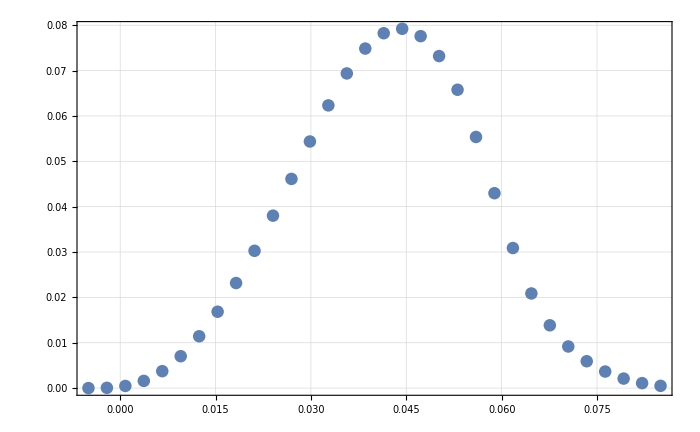

```mathematica
ListPlot[
Transpose[{-Reverse[XDatam85p05Bins32],ProtonILLData180WFilter[[All,2]]}]
]
```

```mathematica
Export["~/Dropbox/PhD/ProtonILLData_180WFilter_Xm85p05_32Bins.txt", Transpose[{-Reverse[XDatam85p05Bins32],ProtonILLData180WFilter[[All,2]]}],"Table"];
```

```mathematica
ProtonILLData180WFilter=Import["~/Dropbox/PhD/ProtonILLData_180WFilter_Xm85p05_48Bins.txt","Table"];
```

### PERC

```mathematica
t0=AbsoluteTime[];
ProtonPERCData180=Table[{bin,ProtonFitFuncBinNormArith[bin,{-0.103,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam70p05Bins32,3]},{bin,1,Length[XDatam70p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.11358 and 0.00111568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.306301 and 0.00036749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00106425 and 0.000365039 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0264506 and 0.0000284506 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00785161 and 0.0000121508 for the integral and error estimates.

453.142977

### 447s

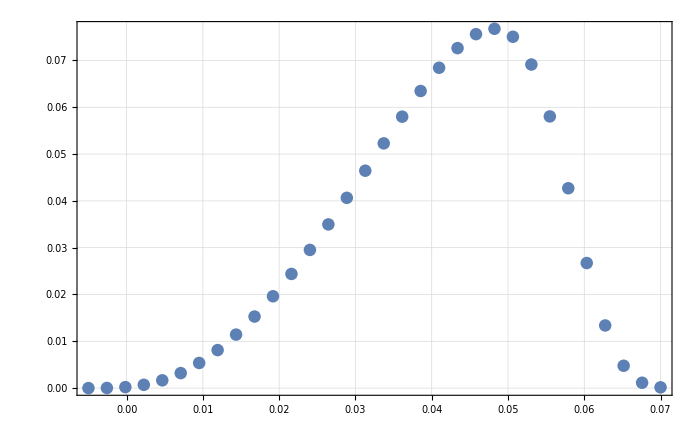

```mathematica
ListPlot[
Transpose[{-Reverse[XDatam70p05Bins32],ProtonPERCData180[[All,2]]}]
]
```

```mathematica
t0=AbsoluteTime[];
ProtonPERCData180a3em3=Table[{bin,ProtonFitFuncBinNormArith[bin,{-0.103+0.103*3*10^-3,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam70p05Bins32,3]},{bin,1,Length[XDatam70p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.11342 and 0.00111551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.306242 and 0.00036742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00106403 and 0.000364962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0264451 and 0.0000284448 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00784997 and 0.0000121483 for the integral and error estimates.

455.989848

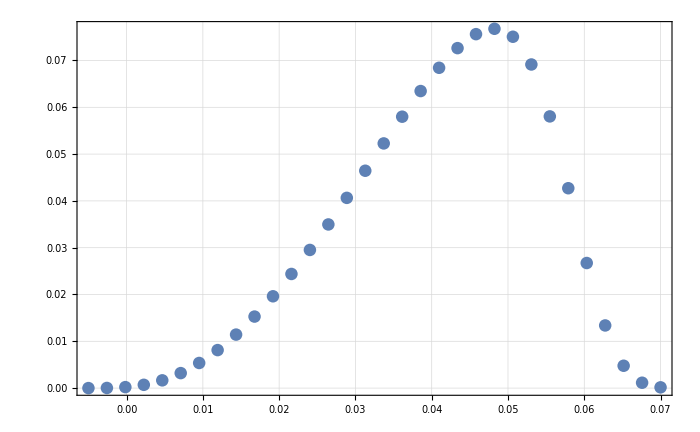

```mathematica
ListPlot[
Transpose[{-Reverse[XDatam70p05Bins32],ProtonPERCData180a3em3[[All,2]]}]
]
```

```mathematica
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonPERCData_180°_Xm70p05_32Bins.txt", Transpose[{-Reverse[XDatam70p05Bins32],ProtonPERCData180[[All,2]]}],"Table"];
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonPERCData_180°_Xm70p05_32Bins_da3e-3.txt", Transpose[{-Reverse[XDatam70p05Bins32],ProtonPERCData180a3em3[[All,2]]}],"Table"];
```

### beginning intermediate transport 18°

```mathematica
XDatam20p05Bins32=XDataCreation[{-0.02,0.005,0.},32]
```

{-0.02,-0.0191935,-0.0183871,-0.0175806,-0.0167742,-0.0159677,-0.0151613,-0.0143548,-0.0135484,-0.0127419,-0.0119355,-0.011129,-0.0103226,-0.00951613,-0.00870968,-0.00790323,-0.00709677,-0.00629032,-0.00548387,-0.00467742,-0.00387097,-0.00306452,-0.00225806,-0.00145161,-0.000645161,0.00016129,0.000967742,0.00177419,0.00258065,0.0033871,0.00419355,0.005}

```mathematica
t0=AbsoluteTime[];
ProtonILLDataBeginWFilter=Table[{bin,ProtonFitFuncBinNormArith[bin,{-0.103,22.5/180*Pi,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam20p05Bins32,3]},{bin,1,Length[XDatam20p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0574316 and 0.0000699561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.325109 and 0.000720932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.540004 and 0.00108128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.68738 and 0.000982558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.874298 and 0.0013203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.12646 and 0.00118851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.44454 and 0.00851936 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.79827 and 0.00305971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.15731 and 0.00222538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.49525 and 0.00335002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7237 and 0.0037887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.38062 and 0.00380921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.00694 and 0.00356134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62973 and 0.00457871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.27475 and 0.00290988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.956533 and 0.00216457 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.687866 and 0.00445566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.476129 and 0.00367611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.216333 and 0.214539 for the integral and error estimates.

548.588536

### 548 s

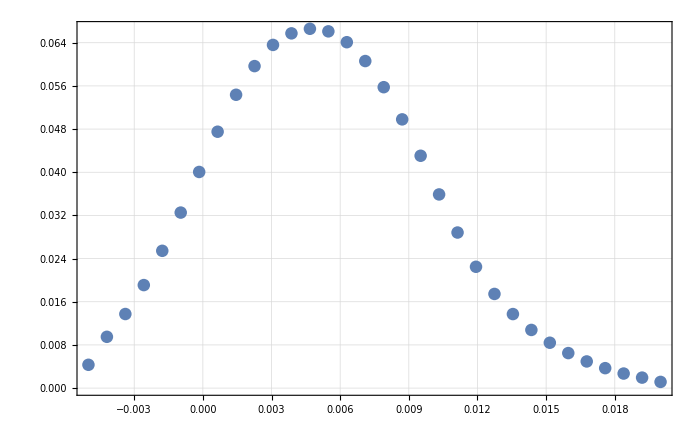

```mathematica
ListPlot[
Transpose[{-Reverse[XDatam20p05Bins32],ProtonILLDataBeginWFilter[[All,2]]}]
]
```

```mathematica
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonILLData_22,5°WFilter_Xm20p05_32Bins.txt", Transpose[{-Reverse[XDatam20p05Bins32],ProtonILLDataBeginWFilter[[All,2]]}],"Table"];
```

```mathematica
t0=AbsoluteTime[];
ProtonILLDataBeginWFilter2=Table[{bin,ProtonFitFuncBinNormArith[bin,{-0.103,2/180*Pi,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam20p05Bins32,3]},{bin,1,Length[XDatam20p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in th0 near {th0,x0,p} = {0.0444613,0.495129,0.844124}. NIntegrate obtained 0.0537489 and 0.00010965 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 16 recursive bisections in th0 near {th0,x0,p} = {0.0444552,0.932629,0.844124}. NIntegrate obtained 0.0461669 and 0.00015893 for the integral and error estimates.

37.7464

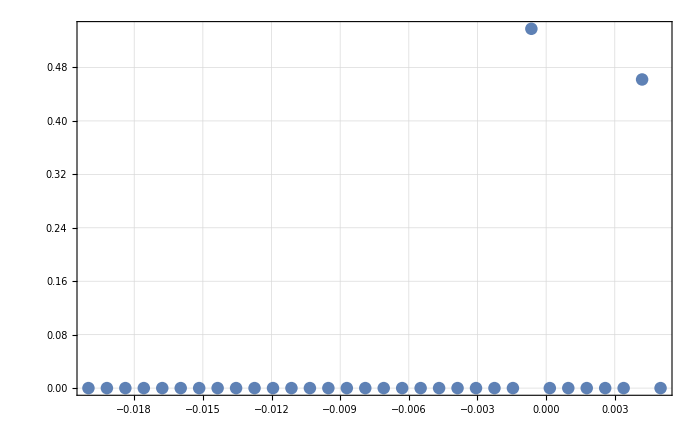

```mathematica
ListPlot[
Transpose[{Reverse[XDatam20p05Bins32],ProtonILLDataBeginWFilter2[[All,2]]}]
]
```

Fits 180° with filter

### ILL

```mathematica
ProtonILLData180WFilter=Transpose[{Table[i,{i,48}],ProtonILLData180WFilter[[All,2]]}]
```

{{1,0.},{2,0.0000112136},{3,0.0000894957},{4,0.000301745},{5,0.00071361},{6,0.00138907},{7,0.00238564},{8,0.00371503},{9,0.00536728},{10,0.00733116},{11,0.00958383},{12,0.0121183},{13,0.0149022},{14,0.0179163},{15,0.0211255},{16,0.0245036},{17,0.028005},{18,0.0315786},{19,0.0351711},{20,0.0386922},{21,0.0420673},{22,0.0451296},{23,0.0477676},{24,0.049863},{25,0.0513329},{26,0.0521274},{27,0.0522026},{28,0.0515249},{29,0.05007},{30,0.0477753},{31,0.0445974},{32,0.040549},{33,0.0356884},{34,0.0302905},{35,0.0248479},{36,0.019742},{37,0.0152692},{38,0.0116503},{39,0.0089024},{40,0.0067954},{41,0.00513834},{42,0.00382916},{43,0.00279699},{44,0.00198798},{45,0.00136462},{46,0.000899734},{47,0.000561919},{48,0.000327274}}

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ILL180WFilterProtondrAFit=Reap[NonlinearModelFit[
ProtonILLData180WFilter,
{
ProtonFitFuncBinNormArith[bin,{a,Pi,0.2,1.,1.,2.,1.+10^-4},{0.01,0.035,0.,0.,0.},XDatam85p05Bins48,3],
-0.1035<a<-0.1025
},
{{a,-0.1031}},bin,MaxIterations->8,EvaluationMonitor:>Sow[a],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 20 Sep 2019 17:20:07

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.8599 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77807 and 0.00290998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75957 and 0.00178904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56047 and 0.0019454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.3654 and 0.00167233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17718 and 0.00118132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998368 and 0.00108948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830415 and 0.000981612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675292 and 0.000722149 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534058 and 0.000965679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408537 and 0.000429903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299099 and 0.000354732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207064 and 0.000279106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132944 and 0.000134071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397673 and 0.0000446052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168156 and 0.0000273762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498755 and 0.0000141883 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624101 and 3.32321×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85991 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77808 and 0.00290999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75961 and 0.00178907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56051 and 0.00194544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36543 and 0.00167238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17721 and 0.00118136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998397 and 0.00108951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.83044 and 0.00098164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675313 and 0.000722172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534076 and 0.000965708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408551 and 0.000429917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.29911 and 0.000354744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207071 and 0.000279116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132948 and 0.000134076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397687 and 0.0000446068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168162 and 0.0000273772 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498773 and 0.0000141888 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624124 and 3.32334×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.8599 and 0.00347016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77807 and 0.00290998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75957 and 0.00178903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56047 and 0.00194539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.3654 and 0.00167233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17718 and 0.00118132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998367 and 0.00108947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830414 and 0.000981611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675291 and 0.000722148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534058 and 0.000965677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408537 and 0.000429903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299099 and 0.000354732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207064 and 0.000279106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132943 and 0.000134071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397672 and 0.0000446052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168155 and 0.0000273762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498754 and 0.0000141883 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0006241 and 3.32321×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.0034735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77799 and 0.00290991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75932 and 0.00178877 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56022 and 0.00194507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36516 and 0.00167202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17696 and 0.00118108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998167 and 0.00108925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830239 and 0.00098141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675142 and 0.000721986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533935 and 0.000965468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.40844 and 0.000429806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299026 and 0.000354645 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207013 and 0.000279038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.13291 and 0.000134037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.039757 and 0.0000445937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168112 and 0.0000273691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498623 and 0.0000141845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623936 and 3.32233×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.8599 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77807 and 0.00290998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75957 and 0.00178904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56048 and 0.0019454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.3654 and 0.00167233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17718 and 0.00118132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.99837 and 0.00108948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830417 and 0.000981614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675294 and 0.00072215 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.53406 and 0.000965681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408538 and 0.000429904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.2991 and 0.000354733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207065 and 0.000279107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132944 and 0.000134071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397674 and 0.0000446053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168156 and 0.0000273763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498756 and 0.0000141883 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624102 and 3.32322×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90421 and 0.00347257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85986 and 0.00347023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7779 and 0.00290984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75902 and 0.00178845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.55993 and 0.00194469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36488 and 0.00167165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1767 and 0.0011808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.997931 and 0.00108899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830032 and 0.000981173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.674966 and 0.000721795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.53379 and 0.000965221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408326 and 0.000429691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.29894 and 0.000354543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206952 and 0.000278958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.13287 and 0.000133998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397448 and 0.0000445802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.016806 and 0.0000273607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498469 and 0.0000141802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623742 and 3.3213×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85991 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77807 and 0.00290998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75958 and 0.00178905 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56048 and 0.00194541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36541 and 0.00167234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17719 and 0.00118133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998377 and 0.00108948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830423 and 0.00098162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675299 and 0.000722156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534063 and 0.000965687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408542 and 0.000429907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299102 and 0.000354736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207066 and 0.000279109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132945 and 0.000134073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397677 and 0.0000446057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168158 and 0.0000273765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0049876 and 0.0000141884 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624108 and 3.32325×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90419 and 0.00348343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85987 and 0.00347021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77793 and 0.00290986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75911 and 0.00178855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56002 and 0.00194481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36497 and 0.00167177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17678 and 0.00118089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998006 and 0.00108907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830098 and 0.000981248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675022 and 0.000721856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533836 and 0.000965299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408362 and 0.000429728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.298968 and 0.000354576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206971 and 0.000278983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132883 and 0.00013401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397487 and 0.0000445845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168076 and 0.0000273634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498518 and 0.0000141815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623803 and 3.32163×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90421 and 0.00347258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85986 and 0.00347023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7779 and 0.00290983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.759 and 0.00178843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.55991 and 0.00194466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36486 and 0.00167163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17668 and 0.00118078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.997915 and 0.00108897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830018 and 0.000981157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.674954 and 0.000721782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533781 and 0.000965204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408318 and 0.000429684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.298935 and 0.000354536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206948 and 0.000278952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132868 and 0.000133995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.039744 and 0.0000445793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168056 and 0.0000273601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498458 and 0.0000141799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623729 and 3.32123×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85991 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77807 and 0.00290998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.7596 and 0.00178907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.5605 and 0.00194543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36542 and 0.00167237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17721 and 0.00118135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.99839 and 0.0010895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830435 and 0.000981634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675309 and 0.000722167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534072 and 0.000965702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408548 and 0.000429914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299107 and 0.000354742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.20707 and 0.000279114 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132947 and 0.000134075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397684 and 0.0000446065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168161 and 0.000027377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498769 and 0.0000141887 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624119 and 3.32331×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90416 and 0.00347347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77801 and 0.00290993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75939 and 0.00178884 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56029 and 0.00194516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36522 and 0.00167211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17702 and 0.00118115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998222 and 0.00108931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830287 and 0.000981465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675183 and 0.00072203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533969 and 0.000965525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408467 and 0.000429832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299046 and 0.000354669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132919 and 0.000134046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207027 and 0.000279057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397598 and 0.0000445968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168124 and 0.000027371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498659 and 0.0000141856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00062398 and 3.32257×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85991 and 0.00347016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77808 and 0.00290999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75961 and 0.00178907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56051 and 0.00194544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36543 and 0.00167238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17721 and 0.00118136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998397 and 0.00108951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830441 and 0.000981641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675314 and 0.000722172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534076 and 0.000965709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408551 and 0.000429917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.29911 and 0.000354745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207072 and 0.000279116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132948 and 0.000134076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397688 and 0.0000446069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168162 and 0.0000273773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498774 and 0.0000141888 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624124 and 3.32334×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85991 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77807 and 0.00290998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75959 and 0.00178906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56049 and 0.00194542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36542 and 0.00167236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1772 and 0.00118134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998384 and 0.00108949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830429 and 0.000981628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675304 and 0.000722162 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534068 and 0.000965695 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408545 and 0.000429911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299105 and 0.000354739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207068 and 0.000279112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132946 and 0.000134074 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397681 and 0.0000446061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168159 and 0.0000273768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498765 and 0.0000141886 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624114 and 3.32328×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90415 and 0.00347344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77803 and 0.00290995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75945 and 0.0017889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56035 and 0.00194524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36528 and 0.00167218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17707 and 0.0011812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.99827 and 0.00108936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830329 and 0.000981513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675219 and 0.000722069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533998 and 0.000965575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.40849 and 0.000429855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299063 and 0.000354689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207039 and 0.000279073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132927 and 0.000134054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397622 and 0.0000445996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0049869 and 0.0000141864 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168134 and 0.0000273727 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00062402 and 3.32278×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.00347349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77799 and 0.00290992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75933 and 0.00178878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56024 and 0.00194509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36517 and 0.00167204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17697 and 0.00118109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998179 and 0.00108926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830249 and 0.000981422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675151 and 0.000721995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533942 and 0.00096548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408446 and 0.000429811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.29903 and 0.00035465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207015 and 0.000279042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132912 and 0.000134039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397575 and 0.0000445944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168114 and 0.0000273695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498631 and 0.0000141848 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623945 and 3.32238×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.8599 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77807 and 0.00290998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75957 and 0.00178903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56047 and 0.00194539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.3654 and 0.00167233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17718 and 0.00118132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998367 and 0.00108947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830414 and 0.00098161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675291 and 0.000722147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534057 and 0.000965677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408537 and 0.000429902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299099 and 0.000354731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207064 and 0.000279106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132943 and 0.000134071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397672 and 0.0000446051 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168155 and 0.0000273762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498754 and 0.0000141882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624099 and 3.32321×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85991 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77808 and 0.00290999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75961 and 0.00178908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56052 and 0.00194545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36544 and 0.00167238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17722 and 0.00118136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998402 and 0.00108951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830445 and 0.000981646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675317 and 0.000722176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534079 and 0.000965714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408554 and 0.000429919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299112 and 0.000354747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207073 and 0.000279118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132949 and 0.000134077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.039769 and 0.0000446071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168163 and 0.0000273774 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498777 and 0.0000141889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624128 and 3.32336×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90418 and 0.00348339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85987 and 0.00347021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77795 and 0.00290988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.7592 and 0.00178864 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.5601 and 0.00194491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36504 and 0.00167187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17685 and 0.00118096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998071 and 0.00108914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830154 and 0.000981313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.67507 and 0.000721908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533876 and 0.000965367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408393 and 0.000429759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.298991 and 0.000354603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206988 and 0.000279005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132894 and 0.000134021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.039752 and 0.0000445882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.016809 and 0.0000273656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0049856 and 0.0000141827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623856 and 3.32191×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90415 and 0.00347344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.8599 and 0.00347018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77804 and 0.00290995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75947 and 0.00178893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56037 and 0.00194526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.3653 and 0.0016722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17709 and 0.00118122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998286 and 0.00108938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830343 and 0.000981529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675231 and 0.000722082 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534008 and 0.000965593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408498 and 0.000429863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299069 and 0.000354697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207043 and 0.000279078 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.13293 and 0.000134057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397631 and 0.0000446005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168138 and 0.0000273733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498701 and 0.0000141868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624033 and 3.32285×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90416 and 0.00347348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77801 and 0.00290993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75937 and 0.00178882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56028 and 0.00194514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36521 and 0.00167209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17701 and 0.00118113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.99821 and 0.0010893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830277 and 0.000981453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675174 and 0.000722021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533962 and 0.000965513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408461 and 0.000429827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299042 and 0.000354664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207024 and 0.000279053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132917 and 0.000134045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397592 and 0.0000445962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168121 and 0.0000273706 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498651 and 0.0000141853 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623971 and 3.32252×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90416 and 0.00347346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77801 and 0.00290993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.7594 and 0.00178885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.5603 and 0.00194517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36523 and 0.00167212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17703 and 0.00118116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998232 and 0.00108932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830295 and 0.000981475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.67519 and 0.000722038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533975 and 0.000965535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408471 and 0.000429837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.29905 and 0.000354673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207029 and 0.00027906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132921 and 0.000134048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397603 and 0.0000445974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168126 and 0.0000273714 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498665 and 0.0000141857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623988 and 3.32261×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90415 and 0.00347346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77802 and 0.00290994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75941 and 0.00178887 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56032 and 0.00194519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36525 and 0.00167214 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17704 and 0.00118117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998242 and 0.00108933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830305 and 0.000981485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675198 and 0.000722047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533981 and 0.000965546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408476 and 0.000429842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299053 and 0.000354678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132922 and 0.00013405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207032 and 0.000279063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397608 and 0.000044598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498672 and 0.0000141859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168128 and 0.0000273717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623997 and 3.32266×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90418 and 0.00348338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.0034702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77796 and 0.00290989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75922 and 0.00178867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56013 and 0.00194495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36507 and 0.0016719 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17688 and 0.00118099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998093 and 0.00108917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830173 and 0.000981335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675087 and 0.000721926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533889 and 0.00096539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408404 and 0.00042977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.298999 and 0.000354613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132897 and 0.000134025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206993 and 0.000279013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397531 and 0.0000445894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168095 and 0.0000273664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498574 and 0.0000141832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623874 and 3.32201×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90418 and 0.0034834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85987 and 0.00347021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77795 and 0.00290988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75918 and 0.00178862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56009 and 0.00194489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36503 and 0.00167185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17684 and 0.00118095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998057 and 0.00108913 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830142 and 0.000981299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.67506 and 0.000721897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533868 and 0.000965353 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408387 and 0.000429752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.298986 and 0.000354598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206984 and 0.000279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132891 and 0.000134019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397513 and 0.0000445874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168087 and 0.0000273652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498551 and 0.0000141825 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623845 and 3.32185×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90421 and 0.00347256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85986 and 0.00347022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7779 and 0.00290984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75903 and 0.00178846 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.55994 and 0.0019447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36489 and 0.00167167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17671 and 0.00118081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.997941 and 0.001089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830041 and 0.000981183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.674974 and 0.000721803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533797 and 0.000965231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408331 and 0.000429696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.298944 and 0.000354548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206954 and 0.000278961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132872 and 0.000133999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397453 and 0.0000445807 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168062 and 0.000027361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498475 and 0.0000141803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00062375 and 3.32134×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85991 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77807 and 0.00290998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.7596 and 0.00178906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.5605 and 0.00194543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36542 and 0.00167236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1772 and 0.00118135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998388 and 0.0010895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830433 and 0.000981632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675307 and 0.000722165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534071 and 0.0009657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408547 and 0.000429913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299107 and 0.000354741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207069 and 0.000279113 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132947 and 0.000134074 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397683 and 0.0000446064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.016816 and 0.0000273769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498768 and 0.0000141887 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624117 and 3.3233×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90418 and 0.00348338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.0034702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77796 and 0.00290989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75923 and 0.00178867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56014 and 0.00194495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36507 and 0.00167191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17688 and 0.001181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998097 and 0.00108917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830177 and 0.000981339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675089 and 0.000721929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533892 and 0.000965394 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408406 and 0.000429771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299 and 0.000354615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206994 and 0.000279014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397533 and 0.0000445896 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132898 and 0.000134025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623877 and 3.32202×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498577 and 0.0000141832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168096 and 0.0000273666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90413 and 0.00347339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.8599 and 0.00347016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77806 and 0.00290997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75956 and 0.00178903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56047 and 0.00194539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36539 and 0.00167232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17717 and 0.00118132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998362 and 0.00108947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.83041 and 0.000981606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675288 and 0.000722144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534055 and 0.000965672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408534 and 0.0004299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299097 and 0.000354729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207063 and 0.000279104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132943 and 0.00013407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.039767 and 0.0000446049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168154 and 0.000027376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498751 and 0.0000141882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624096 and 3.32319×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.00347349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77799 and 0.00290992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75933 and 0.00178878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56024 and 0.00194509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36517 and 0.00167204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17697 and 0.00118109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998177 and 0.00108926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830248 and 0.00098142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.67515 and 0.000721994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533941 and 0.000965478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408445 and 0.000429811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.29903 and 0.000354649 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132912 and 0.000134039 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207015 and 0.000279041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397575 and 0.0000445943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168114 and 0.0000273694 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0049863 and 0.0000141847 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623944 and 3.32238×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90418 and 0.00348338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.0034702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77796 and 0.00290989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75923 and 0.00178867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56013 and 0.00194495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36507 and 0.00167191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17688 and 0.00118099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998096 and 0.00108917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830176 and 0.000981338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675089 and 0.000721928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533891 and 0.000965393 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408406 and 0.000429771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299 and 0.000354614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206994 and 0.000279014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132898 and 0.000134025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397533 and 0.0000445896 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168096 and 0.0000273665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498576 and 0.0000141832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623877 and 3.32202×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90415 and 0.00347344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77803 and 0.00290995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75945 and 0.0017889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56035 and 0.00194524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36528 and 0.00167218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17707 and 0.0011812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.99827 and 0.00108936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830329 and 0.000981513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675219 and 0.000722069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533998 and 0.000965575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.40849 and 0.000429855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299063 and 0.000354689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207039 and 0.000279073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132927 and 0.000134054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397622 and 0.0000445996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168134 and 0.0000273727 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0049869 and 0.0000141864 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00062402 and 3.32278×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.0034735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77799 and 0.00290991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75931 and 0.00178876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56022 and 0.00194506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36515 and 0.00167201 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17695 and 0.00118107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998162 and 0.00108924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830234 and 0.000981404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675138 and 0.000721981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533932 and 0.000965462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408437 and 0.000429803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299024 and 0.000354643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207011 and 0.000279036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132909 and 0.000134036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397567 and 0.0000445934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.016811 and 0.0000273689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498619 and 0.0000141844 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623931 and 3.32231×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90419 and 0.00348341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85987 and 0.00347021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77794 and 0.00290987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75914 and 0.00178858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56005 and 0.00194485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36499 and 0.00167181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17681 and 0.00118092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.99803 and 0.0010891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830119 and 0.000981272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.67504 and 0.000721875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533851 and 0.000965325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408374 and 0.000429739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.298976 and 0.000354586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206977 and 0.000278991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132887 and 0.000134014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397499 and 0.0000445858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168082 and 0.0000273642 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498534 and 0.000014182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623823 and 3.32173×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.00347351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.0034702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77798 and 0.0029099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75928 and 0.00178873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56019 and 0.00194502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36512 and 0.00167198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17693 and 0.00118105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998138 and 0.00108922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830213 and 0.000981381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675121 and 0.000721962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533917 and 0.000965438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408426 and 0.000429792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299016 and 0.000354633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207005 and 0.000279028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132905 and 0.000134032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397555 and 0.000044592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168105 and 0.0000273681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498604 and 0.000014184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623912 and 3.32221×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90415 and 0.00347344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77803 and 0.00290995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75945 and 0.00178891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56036 and 0.00194524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36529 and 0.00167219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17708 and 0.00118121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998274 and 0.00108937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830332 and 0.000981517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675222 and 0.000722072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534 and 0.00096558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408492 and 0.000429857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299065 and 0.000354691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.20704 and 0.000279074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132928 and 0.000134055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397624 and 0.0000445998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168135 and 0.0000273729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498693 and 0.0000141865 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624023 and 3.3228×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.00347349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77799 and 0.00290992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75933 and 0.00178878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56024 and 0.00194509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36517 and 0.00167204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17697 and 0.00118109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998178 and 0.00108926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830248 and 0.000981421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.67515 and 0.000721994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533941 and 0.000965479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408445 and 0.000429811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.29903 and 0.00035465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207015 and 0.000279041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132912 and 0.000134039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397575 and 0.0000445943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168114 and 0.0000273695 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0049863 and 0.0000141847 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623944 and 3.32238×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.00348337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.0034702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77797 and 0.00290989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75924 and 0.00178868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56014 and 0.00194496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36508 and 0.00167192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17689 and 0.001181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998102 and 0.00108918 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830182 and 0.000981345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675094 and 0.000721933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533895 and 0.0009654 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408409 and 0.000429774 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299003 and 0.000354617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206996 and 0.000279016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132899 and 0.000134026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397536 and 0.00004459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168097 and 0.0000273668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498581 and 0.0000141833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623882 and 3.32205×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90419 and 0.00348341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85987 and 0.00347021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77794 and 0.00290987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75916 and 0.0017886 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56007 and 0.00194487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36501 and 0.00167183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17682 and 0.00118093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998043 and 0.00108911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.83013 and 0.000981285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.67505 and 0.000721885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533859 and 0.000965338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.40838 and 0.000429746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.298981 and 0.000354592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206981 and 0.000278996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132889 and 0.000134016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397506 and 0.0000445866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168084 and 0.0000273647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498542 and 0.0000141822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623834 and 3.32179×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.00347352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.0034702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77798 and 0.0029099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75928 and 0.00178872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56019 and 0.00194502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36512 and 0.00167197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17692 and 0.00118104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998136 and 0.00108922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830212 and 0.000981379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675119 and 0.000721961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533916 and 0.000965436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408425 and 0.000429791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299015 and 0.000354632 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207005 and 0.000279027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132905 and 0.000134032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397554 and 0.0000445919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168105 and 0.000027368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498603 and 0.000014184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00062391 and 3.3222×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.00348336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.0034702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77798 and 0.0029099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75927 and 0.00178871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56018 and 0.00194501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36511 and 0.00167196 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17692 and 0.00118103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998129 and 0.00108921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830205 and 0.000981371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675113 and 0.000721955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533911 and 0.000965428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408421 and 0.000429787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299012 and 0.000354628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207003 and 0.000279025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132903 and 0.000134031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.039755 and 0.0000445915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168103 and 0.0000273677 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498598 and 0.0000141838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623904 and 3.32216×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90416 and 0.00347348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.778 and 0.00290992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75935 and 0.0017888 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56026 and 0.00194511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36519 and 0.00167206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17699 and 0.00118111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998193 and 0.00108928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830262 and 0.000981436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675162 and 0.000722007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533951 and 0.000965495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408453 and 0.000429818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299036 and 0.000354656 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207019 and 0.000279047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132914 and 0.000134042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397583 and 0.0000445952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168117 and 0.00002737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0049864 and 0.000014185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623957 and 3.32245×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90416 and 0.00347349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.778 and 0.00290992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75935 and 0.0017888 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56025 and 0.00194511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36519 and 0.00167206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17698 and 0.00118111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998191 and 0.00108928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.83026 and 0.000981434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.67516 and 0.000722005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.53395 and 0.000965493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408452 and 0.000429817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299035 and 0.000354655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207019 and 0.000279046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132914 and 0.000134041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397582 and 0.000044595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168117 and 0.0000273699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498639 and 0.000014185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623955 and 3.32244×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.0034735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.00347019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77799 and 0.00290991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75931 and 0.00178876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56022 and 0.00194506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36515 and 0.00167202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17696 and 0.00118108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998164 and 0.00108925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830236 and 0.000981407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.67514 and 0.000721983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533933 and 0.000965465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408439 and 0.000429804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299025 and 0.000354644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207012 and 0.000279037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132909 and 0.000134037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397568 and 0.0000445935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168111 and 0.000027369 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498621 and 0.0000141845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623933 and 3.32232×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.00347351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77799 and 0.00290991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.7593 and 0.00178875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56021 and 0.00194505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36514 and 0.001672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17694 and 0.00118107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998155 and 0.00108924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830228 and 0.000981397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675133 and 0.000721976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533927 and 0.000965455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408434 and 0.0004298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299022 and 0.00035464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207009 and 0.000279034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132908 and 0.000134035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397563 and 0.000044593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168109 and 0.0000273686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498615 and 0.0000141843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623925 and 3.32228×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90416 and 0.00347347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77801 and 0.00290993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.7594 and 0.00178885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.5603 and 0.00194517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36523 and 0.00167212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17703 and 0.00118116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998229 and 0.00108932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830293 and 0.000981472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675189 and 0.000722036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533973 and 0.000965533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.40847 and 0.000429836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299049 and 0.000354672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207028 and 0.000279059 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.13292 and 0.000134048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397601 and 0.0000445973 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168125 and 0.0000273713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498664 and 0.0000141857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623987 and 3.32261×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90418 and 0.00348339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85987 and 0.0034702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77796 and 0.00290988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.7592 and 0.00178864 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56011 and 0.00194492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36505 and 0.00167188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17686 and 0.00118097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998077 and 0.00108915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.83016 and 0.000981319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675075 and 0.000721913 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.53388 and 0.000965373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408396 and 0.000429762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.298993 and 0.000354606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.206989 and 0.000279007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132895 and 0.000134022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397523 and 0.0000445885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168092 and 0.0000273659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498564 and 0.0000141829 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623861 and 3.32194×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90415 and 0.00347344 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85989 and 0.00347018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77803 and 0.00290995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.75945 and 0.00178891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56036 and 0.00194524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36529 and 0.00167219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17708 and 0.00118121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998275 and 0.00108937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830333 and 0.000981518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675222 and 0.000722073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.534001 and 0.000965581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408492 and 0.000429858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299065 and 0.000354692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.20704 and 0.000279074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132928 and 0.000134055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397625 and 0.0000445998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168135 and 0.0000273729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498693 and 0.0000141865 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000624024 and 3.3228×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.90417 and 0.00347351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.85988 and 0.00347019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.77799 and 0.00290991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.7593 and 0.00178875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56021 and 0.00194505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.36514 and 0.001672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.17694 and 0.00118107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.998155 and 0.00108924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.830228 and 0.000981397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.675133 and 0.000721976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.533927 and 0.000965455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.408434 and 0.0004298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.299022 and 0.00035464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.207009 and 0.000279034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.132908 and 0.000134035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0397563 and 0.000044593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0168109 and 0.0000273686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00498615 and 0.0000141843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.000623925 and 3.32228×10^-6 for the integral and error estimates.

32387.53759

### 32387s or 9h

```mathematica
ILL180WFilterProtondrAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.102999 | 6.35398×10^-6 | -16210.2 | 3.14629×10^-160

```mathematica
(ILL180WFilterProtondrAFit[[1]]["BestFitParameters"][[1,2]]+0.103)/0.103/(10^-4)
```

0.0627329

### PERC

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
PERC180WFilterProtondrAFit=Reap[NonlinearModelFit[
ProtonPERCData180WFilter,
{
ProtonFitFuncBinNormArith[bin,{a,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5+0.2/1.5*10^-4},{0.01,0.035,0.,0.,0.},XDatam75p05Bins32,3],
-0.1035<a<-0.1025
},
{{a,-0.1031}},bin,MaxIterations->8,EvaluationMonitor:>Sow[a],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 13 Sep 2019 16:18:27

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85836 and 0.000902627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.032082 and 0.0000331657 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952724 and 0.000014979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119328 and 3.27389×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858504 and 0.00090278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320888 and 0.0000331726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119354 and 3.27459×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952926 and 0.0000149821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858529 and 0.000902806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320899 and 0.0000331738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952961 and 0.0000149827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119358 and 3.27471×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858503 and 0.000902779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320887 and 0.0000331726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119353 and 3.27458×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952925 and 0.0000149821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858325 and 0.000902591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320804 and 0.0000331641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952676 and 0.0000149782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119322 and 3.27372×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858505 and 0.000902782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320888 and 0.0000331727 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952929 and 0.0000149822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119354 and 3.2746×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858116 and 0.000902368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320706 and 0.000033154 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952381 and 0.0000149736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119285 and 3.27271×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858511 and 0.000902788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320891 and 0.000033173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952937 and 0.0000149823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119355 and 3.27462×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858182 and 0.000902439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320737 and 0.0000331572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952474 and 0.0000149751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119297 and 3.27303×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858102 and 0.000902353 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320699 and 0.0000331533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952361 and 0.0000149733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119282 and 3.27264×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858523 and 0.0009028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320897 and 0.0000331736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952954 and 0.0000149826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119357 and 3.27468×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858374 and 0.000902642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320827 and 0.0000331664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952744 and 0.0000149793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119331 and 3.27396×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858529 and 0.000902807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.03209 and 0.0000331739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952962 and 0.0000149827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119358 and 3.27471×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858518 and 0.000902795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320894 and 0.0000331733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952946 and 0.0000149825 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119356 and 3.27466×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858416 and 0.000902687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320847 and 0.0000331684 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952803 and 0.0000149802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119338 and 3.27416×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858336 and 0.000902601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320809 and 0.0000331646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0095269 and 0.0000149784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119324 and 3.27377×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858502 and 0.000902778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320887 and 0.0000331726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952924 and 0.0000149821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119353 and 3.27458×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858533 and 0.000902811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320902 and 0.0000331741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119359 and 3.27473×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952968 and 0.0000149828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85824 and 0.0009025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320764 and 0.00003316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952555 and 0.0000149763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119307 and 3.27331×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858431 and 0.000902702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320853 and 0.0000331691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119341 and 3.27424×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952824 and 0.0000149805 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858364 and 0.000902631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320822 and 0.0000331659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952729 and 0.0000149791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119329 and 3.27391×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858382 and 0.000902651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320831 and 0.0000331668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952756 and 0.0000149795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119332 and 3.274×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858392 and 0.000902661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320835 and 0.0000331673 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952769 and 0.0000149797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119334 and 3.27405×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858259 and 0.00090252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320773 and 0.0000331609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0011931 and 3.2734×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952582 and 0.0000149768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858228 and 0.000902487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320758 and 0.0000331594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119305 and 3.27325×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952538 and 0.0000149761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858125 and 0.000902378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.032071 and 0.0000331544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952393 and 0.0000149738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119286 and 3.27275×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858521 and 0.000902798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320896 and 0.0000331735 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119357 and 3.27467×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952951 and 0.0000149825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858262 and 0.000902524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320775 and 0.0000331611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952587 and 0.0000149768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119311 and 3.27342×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858498 and 0.000902774 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320885 and 0.0000331724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952919 and 0.000014982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119353 and 3.27456×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858334 and 0.0009026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320808 and 0.0000331645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952688 and 0.0000149784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119324 and 3.27377×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858262 and 0.000902523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320774 and 0.000033161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952586 and 0.0000149768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119311 and 3.27342×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858416 and 0.000902687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320847 and 0.0000331684 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952803 and 0.0000149802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119338 and 3.27416×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85832 and 0.000902585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320802 and 0.0000331638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952668 and 0.0000149781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.2737×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858204 and 0.000902461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320747 and 0.0000331582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952504 and 0.0000149755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.001193 and 3.27313×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.8583 and 0.000902563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320792 and 0.0000331628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952639 and 0.0000149776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119317 and 3.2736×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85842 and 0.000902691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320848 and 0.0000331686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952808 and 0.0000149803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119339 and 3.27418×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858335 and 0.0009026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320808 and 0.0000331645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952688 and 0.0000149784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119324 and 3.27377×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858267 and 0.000902529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320777 and 0.0000331613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952594 and 0.0000149769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119312 and 3.27344×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858215 and 0.000902474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320752 and 0.0000331588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0095252 and 0.0000149758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119302 and 3.27319×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858298 and 0.000902561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320791 and 0.0000331628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952637 and 0.0000149776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119317 and 3.27359×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858291 and 0.000902554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320788 and 0.0000331624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952627 and 0.0000149775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119316 and 3.27356×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858348 and 0.000902615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320815 and 0.0000331652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952708 and 0.0000149787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119326 and 3.27384×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858346 and 0.000902613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320814 and 0.0000331651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952705 and 0.0000149787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119326 and 3.27383×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858322 and 0.000902587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320803 and 0.0000331639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952671 and 0.0000149781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.27371×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858314 and 0.000902578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320799 and 0.0000331635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952659 and 0.000014978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0011932 and 3.27367×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85838 and 0.000902649 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.032083 and 0.0000331667 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119332 and 3.27399×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952753 and 0.0000149794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858245 and 0.000902505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320766 and 0.0000331602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952563 and 0.0000149764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119308 and 3.27333×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858421 and 0.000902692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320849 and 0.0000331686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952809 and 0.0000149803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119339 and 3.27419×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85832 and 0.000902585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320802 and 0.0000331638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952668 and 0.0000149781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.2737×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85832 and 0.000902585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320802 and 0.0000331638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952668 and 0.0000149781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.2737×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85832 and 0.000902585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320802 and 0.0000331638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952668 and 0.0000149781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.2737×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -1.38833 and 0.00211899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.922342 and 0.00242055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -4.18035 and 0.00439437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.204376 and 0.00021002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.061318 and 0.0000939637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -0.00772638 and 0.0000211445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.922342 and 0.00242055 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -1.38833 and 0.00211899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -4.18035 and 0.00439437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.204376 and 0.00021002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.061318 and 0.0000939637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -0.00772638 and 0.0000211445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85832 and 0.000902585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320802 and 0.0000331638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952668 and 0.0000149781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.2737×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85832 and 0.000902585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320802 and 0.0000331638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.2737×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952668 and 0.0000149781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.51587 and 0.0011287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.455076 and 0.000952527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.66099 and 0.00190219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.0861482 and 0.0000882708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.0258956 and 0.0000395166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -0.00326659 and 8.93758×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.51587 and 0.0011287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.455076 and 0.000952527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.66099 and 0.00190219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.0861482 and 0.0000882708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.0258956 and 0.0000395166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -0.00326659 and 8.93758×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85832 and 0.000902585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320802 and 0.0000331638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952668 and 0.0000149781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.2737×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85832 and 0.000902585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0320802 and 0.0000331638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952668 and 0.0000149781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.2737×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858318 and 0.000902582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.03208 and 0.0000331637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952664 and 0.000014978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.27369×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858317 and 0.000902582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.03208 and 0.0000331637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952664 and 0.000014978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.27369×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858317 and 0.000902582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.03208 and 0.0000331637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952664 and 0.000014978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.27369×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858317 and 0.000902582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.03208 and 0.0000331637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00952664 and 0.000014978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.00119321 and 3.27369×10^-6 for the integral and error estimates.

27225.37378

### 27225s

```mathematica
PERC180WFilterProtondrAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.103007 | 3.81797×10^-6 | -26979.6 | 8.06839×10^-116

```mathematica
(PERC180WFilterProtondrAFit[[1]]["BestFitParameters"][[1,2]]+0.103)/0.103/(10^-4)
```

-0.692206

Data 90 with filter

```mathematica
t0=AbsoluteTime[];
ProtonILLData90WFilter=Table[{bin,ProtonFitFuncBinNormArith[bin,{-0.103,Pi/2,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam55p05Bins48,3]},{bin,1,Length[XDatam55p05Bins48]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0649638 and 0.0183704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.523355 and 0.00081195 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.63704 and 0.000723471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.930627 and 0.00099252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.12397 and 0.00114712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.53473 and 0.00574564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.46274 and 0.00490665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.43139 and 0.00533722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.33824 and 0.00539556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.1911 and 0.00549509 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.99308 and 0.00492343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.75067 and 0.00501325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.4673 and 0.00368717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14831 and 0.00487633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.79853 and 0.00377467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.42003 and 0.00327941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.01996 and 0.00304542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.62109 and 0.0017354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.208474 and 0.000373441 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0888814 and 0.00614936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0263821 and 0.0000641937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00340862 and 0.000181115 for the integral and error estimates.

756.932515

```mathematica
shadowbox[legend_]:=Graphics[{{Gray,Rectangle[{0.05,-0.05},{1.05,0.95}]},{White,EdgeForm[Gray],Rectangle[]},Inset[legend,{0.5,0.5},Center]},ImageSize->100]
```

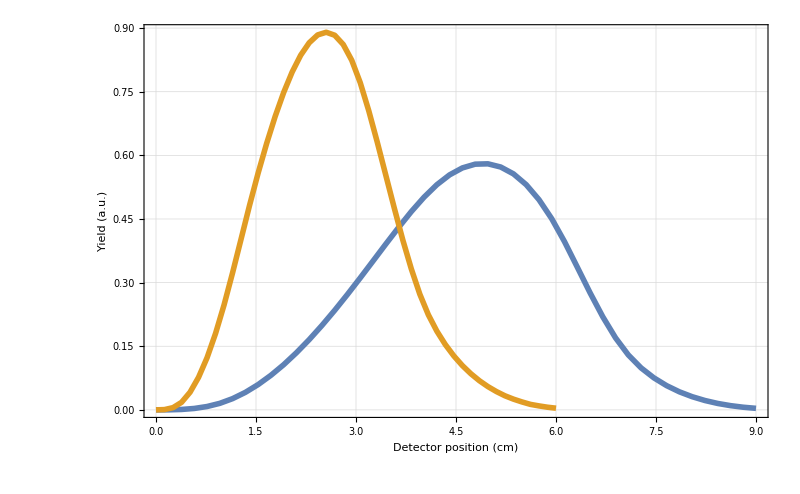

```mathematica
ProtonCompare90W180=ListLinePlot[
{
Transpose[{-Reverse[XDatam85p05Bins48]*100+0.5,ProtonILLData180WFilter[[All,2]]/0.09}],
Transpose[{-Reverse[XDatam55p05Bins48]*100+0.5,ProtonILLData90WFilter[[All,2]]/0.06}]
},GridLines->Automatic,Frame->True,BaseStyle->20,FrameLabel->{{"Yield (a.u.)",None},{"Detector position (cm)","Proton transport spectrum"}},ImageSize->800,PlotStyle->Thickness[0.005],PlotLegends->Placed[LineLegend[{"180°","90°"},LabelStyle->25,LegendFunction->shadowbox,LegendMarkerSize->{20,20},LegendMarkers->Graphics[{Thickness[0.3],Line[{{0,0},{2,0}}]}]],{0.9,0.8}],FrameStyle->Directive[Black,Thick]
]
```

```mathematica
(*Export["~/Dropbox/PhD/ProtonCompare90W180.png",ProtonCompare90W180,ImageResolution->450];*)
```

```mathematica
(*Export["~/Dropbox/PhD/ProtonILLData_90WFilter_Xm55p05_48Bins.txt", Transpose[{-Reverse[XDatam55p05Bins48],ProtonILLData90WFilter[[All,2]]}],"Table"];*)
```

Data 90° no Filter

```mathematica
t0=AbsoluteTime[];
ProtonILLData90noFilter=Table[{bin,ProtonFitFuncBinNormArith[bin,{-0.103,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3]},{bin,1,Length[XDatam55p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233688 and 0.000331781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10475 and 0.00189843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47027 and 0.00201783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45191 and 0.00277418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10453 and 0.0239172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51313 and 0.0181681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61004 and 0.0458017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0126771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8433 and 0.0132279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6443 and 0.0128404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0104857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46533 and 0.0114689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69529 and 0.00896502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92518 and 0.00422904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40672 and 0.00371568 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20647 and 0.00523469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391161 and 0.0160447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511858 and 0.000136353 for the integral and error estimates.

481.008543

### 450s

```mathematica
t0=AbsoluteTime[];
ProtonILLData90noFilteraGoal=Table[{bin,ProtonFitFuncBinNormArith[bin,{-0.103+0.103*2.83*10^-3,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3]},{bin,1,Length[XDatam55p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23373 and 0.000331836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1049 and 0.00189873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47045 and 0.0020181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45216 and 0.00277457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10497 and 0.0239213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51366 and 0.0181701 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61062 and 0.0458039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0126771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8432 and 0.0132278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.644 and 0.0128398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1194 and 0.0183083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2639 and 0.0104899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4647 and 0.0114686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69475 and 0.00896459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92478 and 0.00422885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40645 and 0.00371537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20632 and 0.00523393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391097 and 0.0160424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511761 and 0.000136327 for the integral and error estimates.

788.818193

```mathematica
(*Export["~/Dropbox/PhD/ProtonTransportSpectrum90_aGoal_2,83E-3.txt",Transpose[{-Reverse[XDatam55p05],ProtonILLData90noFilteraGoal[[All,2]]}],"Table"];*)
```

```mathematica
pSpectrum0=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonTransportSpectrum.txt","Table"];
```

```mathematica
eSpectrum0=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronTransportSpectrum.txt","Table"];
```

```mathematica
eSpectrumdb=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronTransportSpectrum90_bGoal_1,16E-3.txt","Table"];
```

```mathematica
pSpectrumda=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ProtonTransportSpectrum90_aGoal_2,83E-3.txt","Table"];
```

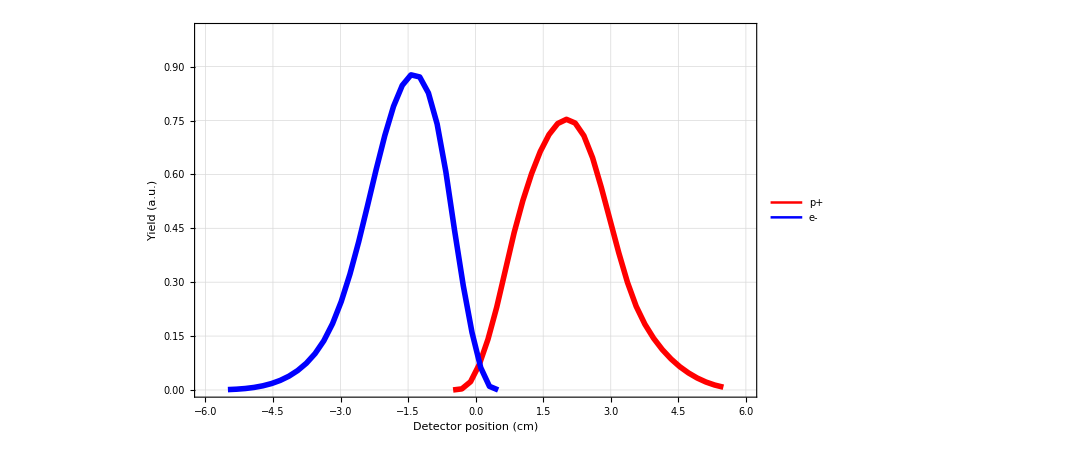

```mathematica
testplot=ListLinePlot[{
Transpose[{-Reverse[XDatam55p05]*100,pSpectrum0[[All,2]]*10}],
Transpose[{eSpectrum0[[All,1]]*100,eSpectrum0[[All,2]]*10}]},Frame->True,GridLines->Automatic,PlotStyle->{Directive[Thickness[0.005],Red],Directive[Thickness[0.005],Blue]},InterpolationOrder->1,FrameStyle->Directive[25,Bold,Black],FrameLabel->{{"Yield (a.u.)",None},{"Detector position (cm)",None}},PlotLegends->Placed[LineLegend[{"p+","e-"},LegendFunction->"Frame",LabelStyle->Directive[25,Bold]],{0.85,0.8}],ImageSize->800,PlotRange->{{-6,6},{0,1}},AspectRatio->1/1.7,ImagePadding->{{110,10},{70,20}}]
```

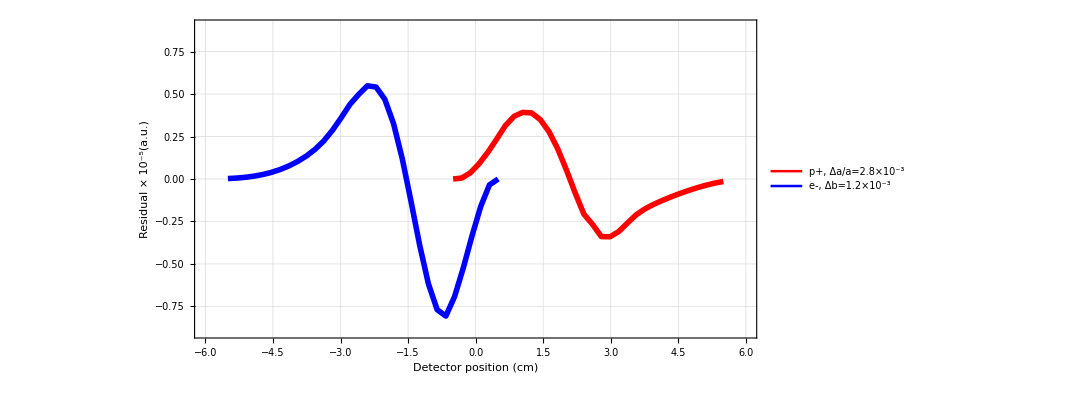

```mathematica
residualplot=ListLinePlot[{
Transpose[{-Reverse[XDatam55p05]*100,(pSpectrum0[[All,2]]-pSpectrumda[[All,2]])*10^5}],
Transpose[{eSpectrum0[[All,1]]*100,(eSpectrum0[[All,2]]-eSpectrumdb[[All,2]])*10^5}]},Frame->True,GridLines->Automatic,PlotStyle->{Directive[Thickness[0.005],Red],Directive[Thickness[0.005],Blue]},InterpolationOrder->1,FrameStyle->Directive[25,Bold,Black],FrameLabel->{{"Residual × 10^-5(a.u.)",None},{"Detector position (cm)",None}},PlotLegends->Placed[LineLegend[{"p+, Δa/a=2.8×10^-3","e-, Δb=1.2×10^-3"},LegendFunction->"Frame",LabelStyle->Directive[25,Bold]],{0.76,0.15}],ImageSize->800,PlotRange->{{-6,6},{-0.9,0.9}},AspectRatio->1/2,ImagePadding->{{110,10},{80,10}}]
```

```mathematica
(*Export["~/Dropbox/PhD/TransportSpectraCompare90_new.png",testplot,ImageResolution->450]
Export["~/Dropbox/PhD/ResidualCompare90_new.png",residualplot,ImageResolution->450]*)
```

~/Dropbox/PhD/TransportSpectraCompare90_new.png

~/Dropbox/PhD/ResidualCompare90_new.png

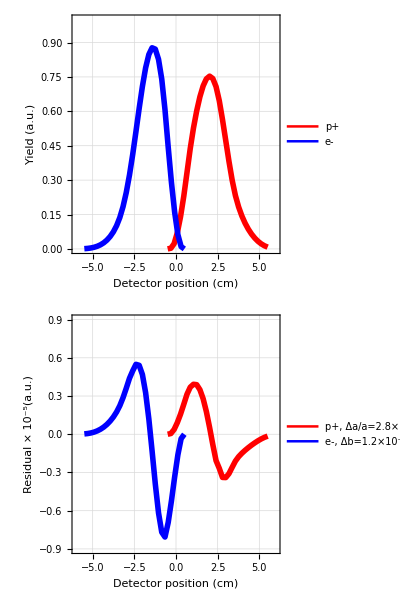

```mathematica
combinedplot=Column[{testplot,residualplot}]
```

```mathematica
(*Export["~/Dropbox/PhD/TransportSpectraCompare90_ultimate.png",combinedplot,ImageResolution->450]*)
```

ItemAspectRatio::shdw: Symbol ItemAspectRatio appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

~/Dropbox/PhD/TransportSpectraCompare90_ultimate.png

```mathematica
t0=AbsoluteTime[];
ProtonPERCData90noFilter=Table[{bin,ProtonFitFuncBinNormArith[bin,{-0.103,Pi/2,0.2,0.2/1.5,0.2/1.5,4,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam55p05,3]},{bin,1,Length[XDatam55p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323837 and 0.00317544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0330457 and 0.0000499302 for the integral and error estimates.

304.815434

### comparison plot with 180° W filter

```mathematica
ProtonILLData180WFilterBins48=Transpose[{XDatam85p05Bins48,ProtonILLData180WFilterBins48[[All,2]]}]
```

{{-0.085,0.},{-0.0830851,0.0000112136},{-0.0811702,0.0000894957},{-0.0792553,0.000301745},{-0.0773404,0.00071361},{-0.0754255,0.00138907},{-0.0735106,0.00238564},{-0.0715957,0.00371503},{-0.0696809,0.00536728},{-0.067766,0.00733116},{-0.0658511,0.00958383},{-0.0639362,0.0121183},{-0.0620213,0.0149022},{-0.0601064,0.0179163},{-0.0581915,0.0211255},{-0.0562766,0.0245036},{-0.0543617,0.028005},{-0.0524468,0.0315786},{-0.0505319,0.0351711},{-0.048617,0.0386922},{-0.0467021,0.0420673},{-0.0447872,0.0451296},{-0.0428723,0.0477676},{-0.0409574,0.049863},{-0.0390426,0.0513329},{-0.0371277,0.0521274},{-0.0352128,0.0522026},{-0.0332979,0.0515249},{-0.031383,0.05007},{-0.0294681,0.0477753},{-0.0275532,0.0445974},{-0.0256383,0.040549},{-0.0237234,0.0356884},{-0.0218085,0.0302905},{-0.0198936,0.0248479},{-0.0179787,0.019742},{-0.0160638,0.0152692},{-0.0141489,0.0116503},{-0.012234,0.0089024},{-0.0103191,0.0067954},{-0.00840426,0.00513834},{-0.00648936,0.00382916},{-0.00457447,0.00279699},{-0.00265957,0.00198798},{-0.000744681,0.00136462},{0.00117021,0.000899734},{0.00308511,0.000561919},{0.005,0.000327274}}

```mathematica
Length[pSpectrum0]
```

32

```mathematica
Length[ProtonILLData180WFilterBins48]
```

48

```mathematica
Total[ProtonILLData180WFilterBins48[[All,2]]]
```

1.

```mathematica
Total[pSpectrum0[[All,2]]]
```

1.

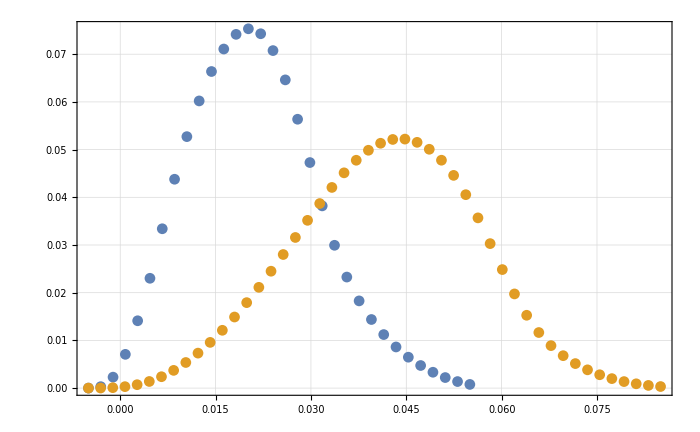

```mathematica
ListPlot[{pSpectrum0,Transpose[{-Reverse[XDatam85p05Bins48],ProtonILLData180WFilterBins48[[All,2]]}]}]
```

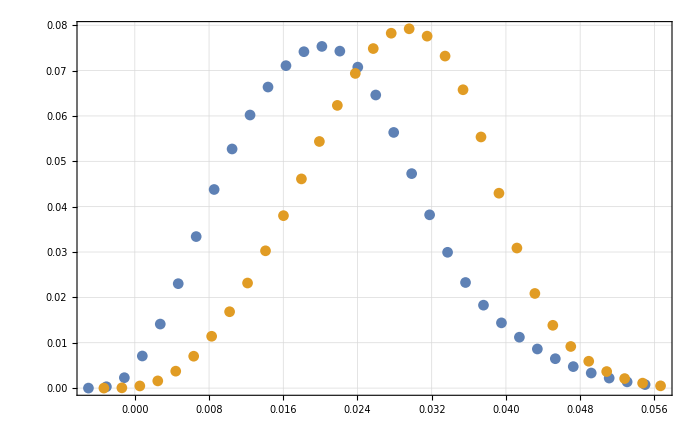

```mathematica
ListPlot[{pSpectrum0,Transpose[{-Reverse[XDatam85p05Bins32]/9*6,ProtonILLData180WFilter[[All,2]]}]}]
```

```mathematica
shadowbox[legend_]:=Graphics[{{White,EdgeForm[Black],Rectangle[{-0.7,-0.4},{0.7,0.4}]},Inset[legend,{0.,0.},Center]},ImageSize->{300,130}]
```

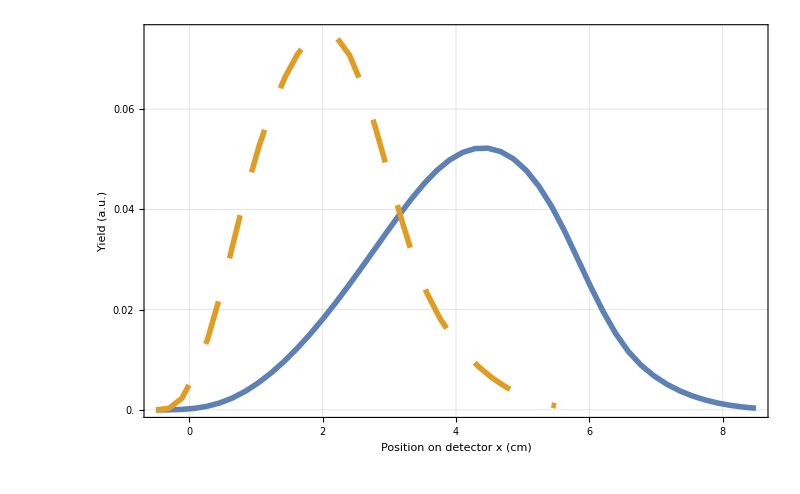

```mathematica
ProtonCompare90W180=ListLinePlot[
{Transpose[{-Reverse[XDatam85p05Bins48]*100,ProtonILLData180WFilterBins48[[All,2]]}],Transpose[{pSpectrum0[[All,1]]*100,pSpectrum0[[All,2]]}]},

GridLines->Automatic,GridLinesStyle->Directive[Thickness[0.002],Black],Frame->True,BaseStyle->25,FrameLabel->{{"Yield (a.u.)",None},{"Position on detector x (cm)","Proton drift distance spectrum"}},ImageSize->{800,600},PlotStyle->{Thickness[0.005],Directive[Thickness[0.005],Dashing[0.04]]},ImagePadding->{{90,10},{80,40}},

PlotLegends->
Placed[
LineLegend[{"180° w filter","90° w/o filter"},LabelStyle->25,LegendFunction->shadowbox,LegendMarkerSize->{30,20},LegendMarkers->{Graphics[{Thickness[0.3],Line[{{0,0},{3,0}}]}],Graphics[{Dashing[{0.4,0.5}],Thickness[0.3],Line[{{0,0},{3,0}}]}]}],
{0.83,0.82}],

FrameTicks->{
{Join[Table[{y,y,{0.02,0.},Thick},{y,0,0.08,0.02}],Table[{y,"",{0.01,0.},Thick},{y,0,0.08,0.005}]],None},
{Join[Table[{y,y,{0.02,0.},Thick},{y,0,9,2}],Table[{y,"",{0.01,0.},Thick},{y,0,9,0.5}]],None}
},

FrameStyle->Directive[Black,Thick],PlotRangePadding->{{0.001,0.001},{0,0.001}}]
```

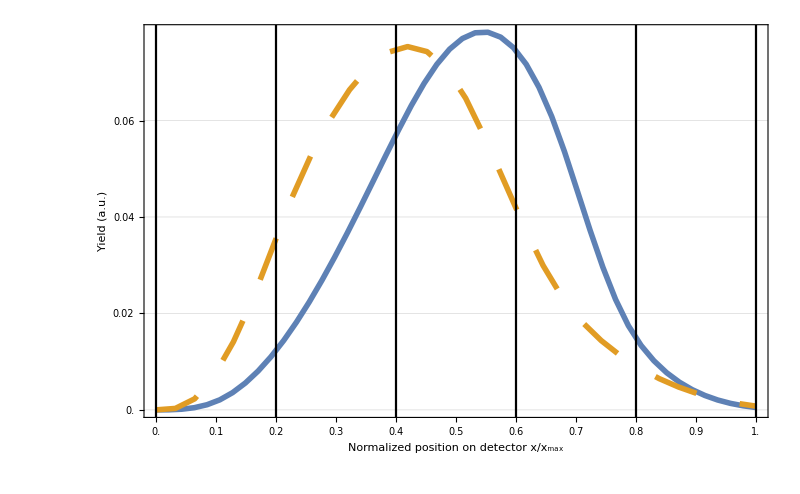

```mathematica
ProtonCompare90W180Rescaled=ListLinePlot[
{Transpose[{(-Reverse[XDatam85p05Bins48]*100+0.5)/9,ProtonILLData180WFilterBins48[[All,2]]/32*48}],Transpose[{(pSpectrum0[[All,1]]*100+0.5)/6,pSpectrum0[[All,2]]}]},

GridLines->{Table[i,{i,0,1,0.2}],Automatic},GridLinesStyle->Directive[Thickness[0.002],Black],Frame->True,BaseStyle->25,FrameLabel->{{"Yield (a.u.)",None},{"Normalized position on detector x/x_max","Rescaled proton drift distance spectrum"}},ImageSize->{800,600},PlotStyle->{Thickness[0.005],Directive[Thickness[0.005],Dashing[0.04]]},ImagePadding->{{90,10},{80,40}},

PlotLegends->
Placed[
LineLegend[{"180° w filter","90° w/o filter"},LabelStyle->25,LegendFunction->shadowbox,LegendMarkerSize->{30,20},LegendMarkers->{Graphics[{Thickness[0.3],Line[{{0,0},{3,0}}]}],Graphics[{Dashing[{0.4,0.5}],Thickness[0.3],Line[{{0,0},{3,0}}]}]}],
{0.83,0.82}],

FrameTicks->{
{Join[Table[{y,y,{0.02,0.},Thick},{y,0,0.08,0.02}],Table[{y,"",{0.01,0.},Thick},{y,0,0.08,0.005}]],None},
{Table[{y,y,{0.02,0.},Thick},{y,0,1,0.1}],None}
},

FrameStyle->Directive[Black,Thick],PlotRangePadding->{{0.001,0.001},{0,0.001}}]
```

```mathematica
(*Export["~/Dropbox/PhD/INPCProceedings/ProtonTransport_Compare180WFilterVS90WOFilter.png",ProtonCompare90W180,ImageResolution->450];
Export["~/Dropbox/PhD/INPCProceedings/ProtonTransport_Compare180WFilterVS90WOFilter_Xrescaled.png",ProtonCompare90W180Rescaled,ImageResolution->450];*)
```

Fits 90° no filter ILL

### dB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ProtondBFit=Reap[NonlinearModelFit[
ProtonILLData90noFilter,
{
ProtonFitFuncBinNormArith[bin,{a,Pi/2,0.2+0.2*5*10^-5,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.1035<a<-0.1025
},
{{a,-0.1031}},bin,MaxIterations->8,EvaluationMonitor:>Sow[a],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 17:18:20

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233532 and 0.000330147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10441 and 0.00188965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46986 and 0.00177958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45144 and 0.0027805 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10387 and 0.0239208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5123 and 0.0181963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60941 and 0.0456856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6456 and 0.0128465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1213 and 0.0181211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.266 and 0.0104892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46652 and 0.0114347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69617 and 0.00901866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92592 and 0.00424895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40707 and 0.00367224 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20672 and 0.00523554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391267 and 0.0160437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511987 and 0.000137493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233487 and 0.000330088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10425 and 0.00188933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46966 and 0.00177929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45117 and 0.00278009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1034 and 0.0239163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51173 and 0.0181941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60879 and 0.0456833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1218 and 0.0181225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2667 and 0.0104899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4672 and 0.011435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69675 and 0.00901913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92635 and 0.00424914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40736 and 0.00367259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20689 and 0.00523636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391336 and 0.0160462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512092 and 0.000137521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23348 and 0.000330078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10422 and 0.00188928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46963 and 0.00177924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45112 and 0.00278001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10332 and 0.0239156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51164 and 0.0181938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60868 and 0.0456829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.646 and 0.0128473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1219 and 0.0181227 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2668 and 0.01049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46732 and 0.0114351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69685 and 0.00901921 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92643 and 0.00424918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40741 and 0.00367265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20692 and 0.0052365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391348 and 0.0160467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051211 and 0.000137526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233488 and 0.000330089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10425 and 0.00188934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46966 and 0.00177929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45117 and 0.00278009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1034 and 0.0239164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51174 and 0.0181942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60879 and 0.0456833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1218 and 0.0181225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2667 and 0.0104899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4672 and 0.011435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69675 and 0.00901913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92635 and 0.00424914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40736 and 0.00367259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20688 and 0.00523635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391335 and 0.0160462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512091 and 0.000137521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233543 and 0.000330161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10444 and 0.00188973 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4699 and 0.00177965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4515 and 0.0027806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10399 and 0.0239219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51244 and 0.0181968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60956 and 0.0456861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6455 and 0.0128463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1212 and 0.0181207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2658 and 0.010489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46635 and 0.0114347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69603 and 0.00901855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92581 and 0.00424891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.407 and 0.00367216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20668 and 0.00523534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.39125 and 0.0160431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511962 and 0.000137486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233487 and 0.000330088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10425 and 0.00188933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46966 and 0.00177928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45116 and 0.00278008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10339 and 0.0239163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51173 and 0.0181941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60878 and 0.0456832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1219 and 0.0181225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2667 and 0.0104899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46721 and 0.011435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69676 and 0.00901914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92636 and 0.00424915 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40736 and 0.00367259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20689 and 0.00523637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391337 and 0.0160463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512093 and 0.000137522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233608 and 0.000330247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10467 and 0.0018902 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47018 and 0.00178008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4519 and 0.0027812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10469 and 0.0239085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51326 and 0.0181999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61046 and 0.0456895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46536 and 0.0114342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69518 and 0.00901787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92518 and 0.00424863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40657 and 0.00367165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20643 and 0.00523402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391149 and 0.0160393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511809 and 0.000137444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233485 and 0.000330085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10424 and 0.00188932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46965 and 0.00177927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45115 and 0.00278006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10338 and 0.0239161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51171 and 0.018194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60876 and 0.0456831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1219 and 0.0181225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2668 and 0.0104899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46724 and 0.0114351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69678 and 0.00901915 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92638 and 0.00424915 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40737 and 0.00367261 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20689 and 0.0052364 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391339 and 0.0160464 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512097 and 0.000137523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233587 and 0.00033022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1046 and 0.00189005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47009 and 0.00177994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45178 and 0.00278101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10447 and 0.0239064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.513 and 0.0181989 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61017 and 0.0456885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8442 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6451 and 0.0128457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1207 and 0.0181193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2651 and 0.0104932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46567 and 0.0114344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69545 and 0.00901808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92538 and 0.00424872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40671 and 0.00367181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20651 and 0.0052344 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391181 and 0.0160405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511857 and 0.000137457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233613 and 0.000330253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10469 and 0.00189023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4702 and 0.0017801 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45193 and 0.00278125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10474 and 0.0239089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51332 and 0.0182002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61052 and 0.0456898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0104928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46529 and 0.0114342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69512 and 0.00901782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92514 and 0.00424861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40654 and 0.00367161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20641 and 0.00523394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391142 and 0.0160391 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511799 and 0.000137441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233481 and 0.000330081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10423 and 0.00188929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46964 and 0.00177925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45113 and 0.00278003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10334 and 0.0239157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51166 and 0.0181939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6087 and 0.0456829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1219 and 0.0181227 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2668 and 0.01049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46729 and 0.0114351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69683 and 0.00901919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92641 and 0.00424917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4074 and 0.00367264 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20691 and 0.00523647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391345 and 0.0160466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512106 and 0.000137525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233528 and 0.000330142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10439 and 0.00188962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46984 and 0.00177955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45141 and 0.00278046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10383 and 0.0239204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51225 and 0.0181961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60935 and 0.0456854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6456 and 0.0128465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1214 and 0.0181212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2661 and 0.0104892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46658 and 0.0114348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69622 and 0.00901871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92596 and 0.00424897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4071 and 0.00367227 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20673 and 0.00523562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391273 and 0.0160439 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511997 and 0.000137495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233479 and 0.000330078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10422 and 0.00188928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46963 and 0.00177923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45112 and 0.00278001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10332 and 0.0239155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51163 and 0.0181938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60868 and 0.0456828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.646 and 0.0128473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1219 and 0.0181227 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2668 and 0.01049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46732 and 0.0114351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69685 and 0.00901921 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92643 and 0.00424918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40741 and 0.00367265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20692 and 0.0052365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391348 and 0.0160467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051211 and 0.000137526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233483 and 0.000330083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10423 and 0.0018893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46964 and 0.00177926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45114 and 0.00278004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10335 and 0.0239159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51168 and 0.0181939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60873 and 0.045683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1219 and 0.0181226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2668 and 0.01049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46727 and 0.0114351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69681 and 0.00901918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9264 and 0.00424916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40739 and 0.00367262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2069 and 0.00523644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391343 and 0.0160465 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512102 and 0.000137524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233515 and 0.000330124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10434 and 0.00188953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46978 and 0.00177947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45133 and 0.00278034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10369 and 0.0239191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51208 and 0.0181955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60917 and 0.0456847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6457 and 0.0128467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1215 and 0.0181216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2663 and 0.0104895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46678 and 0.0114349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6964 and 0.00901884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92609 and 0.00424903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40718 and 0.00367238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20678 and 0.00523586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391294 and 0.0160447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512028 and 0.000137504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23354 and 0.000330157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10443 and 0.00188971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46989 and 0.00177963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45149 and 0.00278057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10396 and 0.0239215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5124 and 0.0181967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60951 and 0.045686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6455 and 0.0128464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1212 and 0.0181208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2659 and 0.0104891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4664 and 0.0114347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69607 and 0.00901858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92584 and 0.00424892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40702 and 0.00367218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20669 and 0.0052354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391255 and 0.0160433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511969 and 0.000137488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233488 and 0.000330089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10425 and 0.00188934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46966 and 0.00177929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45117 and 0.00278009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10341 and 0.0239164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51174 and 0.0181942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6088 and 0.0456833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1218 and 0.0181225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2667 and 0.0104899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46719 and 0.011435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69674 and 0.00901912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92635 and 0.00424914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40736 and 0.00367258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20688 and 0.00523635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391335 and 0.0160462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051209 and 0.000137521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233478 and 0.000330076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10422 and 0.00188927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46962 and 0.00177923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45111 and 0.00278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1033 and 0.0239154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51162 and 0.0181937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60866 and 0.0456828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.646 and 0.0128473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.122 and 0.0181228 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2669 and 0.01049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46734 and 0.0114351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69687 and 0.00901923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92644 and 0.00424918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40742 and 0.00367266 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20692 and 0.00523653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.39135 and 0.0160468 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512113 and 0.000137527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23357 and 0.000330196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10454 and 0.00188992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47002 and 0.00177982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45167 and 0.00278085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10427 and 0.0239245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51277 and 0.0181981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60993 and 0.0456875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6663 and 0.0129743 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8442 and 0.0133092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0128459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1209 and 0.0181199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2654 and 0.0104886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46595 and 0.0114345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69568 and 0.00901827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92555 and 0.00424879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40682 and 0.00367195 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20658 and 0.00523473 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391209 and 0.0160415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511899 and 0.000137469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233604 and 0.000330241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00178005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45188 and 0.00278116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10464 and 0.0239081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5132 and 0.0181997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6104 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46543 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69524 and 0.00901792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92522 and 0.00424865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00367168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.0052341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391156 and 0.0160396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511819 and 0.000137447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233616 and 0.000330257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1047 and 0.00189026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00178013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45195 and 0.00278128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10477 and 0.0239093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51336 and 0.0182003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61057 and 0.0456899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6449 and 0.0128452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181184 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0104927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46524 and 0.0114342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69508 and 0.00901779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9251 and 0.00424859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40652 and 0.00367158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2064 and 0.00523388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391137 and 0.0160389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511791 and 0.000137439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23354 and 0.000330157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10443 and 0.00188971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46989 and 0.00177963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45148 and 0.00278057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10395 and 0.0239215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51239 and 0.0181966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60951 and 0.045686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6455 and 0.0128464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1212 and 0.0181208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2659 and 0.0104891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4664 and 0.0114347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69607 and 0.00901858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92585 and 0.00424892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40702 and 0.00367218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20669 and 0.0052354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391255 and 0.0160433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511969 and 0.000137488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233549 and 0.00033017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10447 and 0.00188978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46993 and 0.00177969 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45154 and 0.00278066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10406 and 0.0239225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51252 and 0.0181971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60964 and 0.0456865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6454 and 0.0128462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1211 and 0.0181205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2657 and 0.0104889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46626 and 0.0114346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69594 and 0.00901848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92575 and 0.00424888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40695 and 0.0036721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20665 and 0.0052351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.39124 and 0.0160427 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511947 and 0.000137482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233615 and 0.000330257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1047 and 0.00189025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47021 and 0.00178012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45195 and 0.00278127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10477 and 0.0239092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51335 and 0.0182003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61056 and 0.0456899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6449 and 0.0128452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0104927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46525 and 0.0114342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69509 and 0.00901779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92511 and 0.0042486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40652 and 0.00367159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2064 and 0.00523389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391138 and 0.0160389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511792 and 0.000137439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233494 and 0.000330097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10427 and 0.00188938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46969 and 0.00177933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4512 and 0.00278014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10347 and 0.023917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51182 and 0.0181945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60888 and 0.0456836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.012974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6458 and 0.0128471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1218 and 0.0181223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2666 and 0.0104898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4671 and 0.011435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69667 and 0.00901906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92629 and 0.00424912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40732 and 0.00367254 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20686 and 0.00523624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391326 and 0.0160459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512077 and 0.000137517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23349 and 0.000330092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10426 and 0.00188935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46968 and 0.00177931 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45118 and 0.00278011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10343 and 0.0239166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51177 and 0.0181943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60883 and 0.0456834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.012974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1218 and 0.0181224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2667 and 0.0104899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46716 and 0.011435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69671 and 0.0090191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92632 and 0.00424913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40734 and 0.00367257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20687 and 0.0052363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391331 and 0.0160461 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512085 and 0.000137519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233573 and 0.000330201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10455 and 0.00188995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47003 and 0.00177985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45169 and 0.00278088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10431 and 0.0239249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51282 and 0.0181983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60998 and 0.0456877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6663 and 0.0129743 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8442 and 0.0133092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0128459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1209 and 0.0181198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2653 and 0.0104885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46589 and 0.0114345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69563 and 0.00901823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92552 and 0.00424878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4068 and 0.00367192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20656 and 0.00523466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391203 and 0.0160413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051189 and 0.000137466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233514 and 0.000330124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10434 and 0.00188953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46978 and 0.00177946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45133 and 0.00278033 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10369 and 0.023919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51207 and 0.0181954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60916 and 0.0456847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6457 and 0.0128468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1215 and 0.0181216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2663 and 0.0104895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46679 and 0.0114349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6964 and 0.00901885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92609 and 0.00424903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40718 and 0.00367238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20678 and 0.00523587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391294 and 0.0160447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512029 and 0.000137504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233565 and 0.000330191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10452 and 0.00188989 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47 and 0.0017798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45164 and 0.00278081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10423 and 0.0239241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51272 and 0.0181979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60987 and 0.0456873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6663 and 0.0129743 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8442 and 0.0133092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.012846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1209 and 0.01812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2655 and 0.0104886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46601 and 0.0114345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69574 and 0.00901832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9256 and 0.00424881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40685 and 0.00367198 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20659 and 0.0052348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391215 and 0.0160418 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511909 and 0.000137471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233548 and 0.000330168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10446 and 0.00188977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46992 and 0.00177968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45154 and 0.00278065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10405 and 0.0239224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5125 and 0.0181971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60963 and 0.0456864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6454 and 0.0128462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1211 and 0.0181206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2657 and 0.0104889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46627 and 0.0114346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69596 and 0.00901849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92576 and 0.00424888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40696 and 0.00367211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20666 and 0.00523512 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391242 and 0.0160428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511949 and 0.000137482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233579 and 0.000330209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10457 and 0.00188999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47006 and 0.00177989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45173 and 0.00278094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10437 and 0.0239255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5129 and 0.0181986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61006 and 0.045688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6663 and 0.0129743 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8442 and 0.0133092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6452 and 0.0128458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1208 and 0.0181196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2652 and 0.0104933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4658 and 0.0114344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69556 and 0.00901817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92546 and 0.00424875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40676 and 0.00367187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20654 and 0.00523455 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391194 and 0.016041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511876 and 0.000137463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233542 and 0.00033016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10444 and 0.00188972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4699 and 0.00177964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4515 and 0.00278059 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10398 and 0.0239217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51242 and 0.0181968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60954 and 0.0456861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6455 and 0.0128463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1212 and 0.0181208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2658 and 0.010489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46637 and 0.0114347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69604 and 0.00901856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92582 and 0.00424891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.407 and 0.00367216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20668 and 0.00523536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391252 and 0.0160431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511964 and 0.000137486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233605 and 0.000330242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47017 and 0.00178005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45188 and 0.00278117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10465 and 0.0239082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51322 and 0.0181998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61041 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46541 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69523 and 0.00901791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92521 and 0.00424864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40659 and 0.00367167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20644 and 0.00523409 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391155 and 0.0160395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511817 and 0.000137446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233555 and 0.000330177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10448 and 0.00188982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46995 and 0.00177973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45158 and 0.00278071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10411 and 0.023923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51258 and 0.0181974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60972 and 0.0456868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8442 and 0.0133092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6454 and 0.0128461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1211 and 0.0181204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2656 and 0.0104888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46617 and 0.0114346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69588 and 0.00901843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9257 and 0.00424886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40692 and 0.00367206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20663 and 0.005235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391232 and 0.0160424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511934 and 0.000137478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233606 and 0.000330244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10467 and 0.00189019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47017 and 0.00178006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45189 and 0.00278119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10467 and 0.0239083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51323 and 0.0181998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61043 and 0.0456894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46539 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69521 and 0.00901789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9252 and 0.00424864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40658 and 0.00367166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20644 and 0.00523406 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391152 and 0.0160395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511814 and 0.000137445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233514 and 0.000330124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10434 and 0.00188953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46978 and 0.00177946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45133 and 0.00278033 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10368 and 0.023919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51207 and 0.0181954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60916 and 0.0456846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6457 and 0.0128468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1215 and 0.0181216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2663 and 0.0104895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46679 and 0.0114349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6964 and 0.00901885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92609 and 0.00424903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40718 and 0.00367238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20679 and 0.00523587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391295 and 0.0160447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512029 and 0.000137504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23361 and 0.00033025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10468 and 0.00189022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47019 and 0.00178009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45191 and 0.00278122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10471 and 0.0239087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51328 and 0.0182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61048 and 0.0456896 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0104928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46533 and 0.0114342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69516 and 0.00901785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92516 and 0.00424862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40656 and 0.00367163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20642 and 0.00523399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391146 and 0.0160392 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511804 and 0.000137443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233612 and 0.000330252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10469 and 0.00189023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4702 and 0.0017801 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45193 and 0.00278124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10474 and 0.0239089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51331 and 0.0182001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61052 and 0.0456897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0104928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46529 and 0.0114342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69513 and 0.00901782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92514 and 0.00424861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40654 and 0.00367161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20641 and 0.00523395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391143 and 0.0160391 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511799 and 0.000137441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233609 and 0.000330248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10468 and 0.00189021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47019 and 0.00178008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45191 and 0.00278121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1047 and 0.0239086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51327 and 0.0182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61047 and 0.0456896 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0104928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46534 and 0.0114342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69517 and 0.00901786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92517 and 0.00424862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40656 and 0.00367164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20643 and 0.005234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391147 and 0.0160393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511806 and 0.000137443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23348 and 0.000330079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10422 and 0.00188928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46963 and 0.00177924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45112 and 0.00278002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10333 and 0.0239156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51164 and 0.0181938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60869 and 0.0456829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1219 and 0.0181227 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2668 and 0.01049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46731 and 0.0114351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69684 and 0.0090192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92642 and 0.00424917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40741 and 0.00367264 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20691 and 0.00523649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391347 and 0.0160467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512108 and 0.000137526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233485 and 0.000330085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10424 and 0.00188931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46965 and 0.00177927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45115 and 0.00278006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10337 and 0.0239161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5117 and 0.018194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60875 and 0.0456831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8444 and 0.0133094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6459 and 0.0128472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1219 and 0.0181226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2668 and 0.0104899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46724 and 0.0114351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69679 and 0.00901916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92638 and 0.00424915 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40738 and 0.00367261 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2069 and 0.00523641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.39134 and 0.0160464 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0512098 and 0.000137523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233582 and 0.000330212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10458 and 0.00189001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47007 and 0.0017799 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45174 and 0.00278096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1044 and 0.0239257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51293 and 0.0181987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61009 and 0.0456882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6663 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8442 and 0.0133092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6452 and 0.0128457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1208 and 0.0181195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2652 and 0.0104933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46576 and 0.0114344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69553 and 0.00901815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92544 and 0.00424874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40674 and 0.00367185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20653 and 0.00523451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.39119 and 0.0160409 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511871 and 0.000137461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233541 and 0.000330159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10444 and 0.00188972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46989 and 0.00177964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45149 and 0.00278058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10397 and 0.0239217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51241 and 0.0181967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60953 and 0.0456861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6455 and 0.0128463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1212 and 0.0181208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2659 and 0.010489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46638 and 0.0114347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69605 and 0.00901857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92583 and 0.00424891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40701 and 0.00367217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20668 and 0.00523537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391253 and 0.0160432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511966 and 0.000137487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233537 and 0.000330153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10442 and 0.00188969 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46987 and 0.00177961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45147 and 0.00278054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10392 and 0.0239212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51236 and 0.0181965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60947 and 0.0456858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8443 and 0.0133093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6455 and 0.0128464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1213 and 0.0181209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2659 and 0.0104891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46645 and 0.0114347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69611 and 0.00901862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92587 and 0.00424893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40704 and 0.0036722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2067 and 0.00523546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.39126 and 0.0160434 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511977 and 0.00013749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233607 and 0.000330245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10467 and 0.00189019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47018 and 0.00178007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4519 and 0.00278119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10468 and 0.0239084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51325 and 0.0181999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61044 and 0.0456895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46538 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6952 and 0.00901788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92519 and 0.00424863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40658 and 0.00367165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20643 and 0.00523404 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391151 and 0.0160394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511812 and 0.000137445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233605 and 0.000330243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47017 and 0.00178005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45188 and 0.00278117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10466 and 0.0239082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51322 and 0.0181998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61041 and 0.0456894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46541 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69522 and 0.0090179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92521 and 0.00424864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40659 and 0.00367167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20644 and 0.00523408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391154 and 0.0160395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511817 and 0.000137446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233606 and 0.000330244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47017 and 0.00178006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45189 and 0.00278118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10466 and 0.0239082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51323 and 0.0181998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61042 and 0.0456894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4654 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69521 and 0.0090179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9252 and 0.00424864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40659 and 0.00367167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20644 and 0.00523407 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391153 and 0.0160395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511815 and 0.000137446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233603 and 0.000330241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00178004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45187 and 0.00278116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10464 and 0.023908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5132 and 0.0181997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61039 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46543 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69524 and 0.00901792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92523 and 0.00424865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00367168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.00523411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391156 and 0.0160396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051182 and 0.000137447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233606 and 0.000330245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10467 and 0.00189019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47018 and 0.00178006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45189 and 0.00278119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10467 and 0.0239083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51324 and 0.0181999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61044 and 0.0456894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46538 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6952 and 0.00901789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9252 and 0.00424864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40658 and 0.00367166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20644 and 0.00523405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391152 and 0.0160394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511813 and 0.000137445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233603 and 0.000330241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00178004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45187 and 0.00278116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10464 and 0.023908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5132 and 0.0181997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61039 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46543 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69524 and 0.00901792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92523 and 0.00424865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00367168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.00523411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391156 and 0.0160396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051182 and 0.000137447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233603 and 0.000330241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00178004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45187 and 0.00278116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10464 and 0.023908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5132 and 0.0181997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61039 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46543 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69524 and 0.00901792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92523 and 0.00424865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00367168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.00523411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391156 and 0.0160396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051182 and 0.000137447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233603 and 0.000330241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00178004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45187 and 0.00278116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10464 and 0.023908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5132 and 0.0181997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61039 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46543 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69524 and 0.00901792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92523 and 0.00424865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00367168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.00523411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391156 and 0.0160396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051182 and 0.000137447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -1.33494 and 0.00158871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.73357 and 0.00469906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -3.54784 and 0.00616019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -4.40144 and 0.00942359 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -6.19325 and 0.0124434 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -5.28751 and 0.00807104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -7.13624 and 0.0120641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -8.18191 and 0.0121071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -9.55364 and 0.013961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -11.5386 and 0.0184645 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -13.3169 and 0.0183531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -13.7409 and 0.0190754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -12.0858 and 0.0259408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -7.95153 and 0.0283618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.1013 and 0.0418445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.57924 and 0.0598697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4548 and 0.0392826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 24.2875 and 0.0500629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 30.271 and 0.0937057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 34.0343 and 0.0535095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 35.4149 and 0.0696573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 34.4439 and 0.0527286 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 31.4124 and 0.0444552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 26.0858 and 0.0296908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.657 and 0.0178542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.13024 and 0.0358414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.81656 and 0.105152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.418681 and 0.00114131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.73357 and 0.00469906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -1.33494 and 0.00158871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -3.54784 and 0.00616019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -4.40144 and 0.00942359 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -6.19325 and 0.0124434 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -5.28751 and 0.00807104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -7.13624 and 0.0120641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -8.18191 and 0.0121071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -9.55364 and 0.013961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -11.5386 and 0.0184645 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -13.3169 and 0.0183531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -13.7409 and 0.0190754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -12.0858 and 0.0259408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -7.95153 and 0.0283618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.1013 and 0.0418445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.57924 and 0.0598697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4548 and 0.0392826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 24.2875 and 0.0500629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 30.271 and 0.0937057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 34.0343 and 0.0535095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 35.4149 and 0.0696572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 34.4439 and 0.0527286 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 31.4124 and 0.0444552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 26.0858 and 0.0296908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.657 and 0.0178542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.13024 and 0.0358414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.81656 and 0.105152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.418681 and 0.00114131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233603 and 0.000330241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00178004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45187 and 0.00278116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10464 and 0.023908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5132 and 0.0181997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61039 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46543 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69524 and 0.00901792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92523 and 0.00424865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00367168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.00523411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391156 and 0.0160396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051182 and 0.000137447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233603 and 0.000330241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00178004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45187 and 0.00278116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10464 and 0.023908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5132 and 0.0181997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61039 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46543 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69524 and 0.00901792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92523 and 0.00424865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00367168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.00523411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391156 and 0.0160396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051182 and 0.000137447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.07224 and 0.00124652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -0.550672 and 0.000618797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.64859 and 0.00444589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.90879 and 0.00330352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -2.13998 and 0.00507805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.34201 and 0.00516811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.5325 and 0.00514071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.79193 and 0.00476876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -3.21493 and 0.00757678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -3.40166 and 0.00738523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.83228 and 0.00834754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.23563 and 0.0206649 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.52851 and 0.0209155 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.48225 and 0.0234999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1173 and 0.0313786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.6475 and 0.0226195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 18.4647 and 0.0278043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 21.2083 and 0.054432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 22.6854 and 0.0294986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 22.8389 and 0.0363317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.712 and 0.0329882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.2907 and 0.0242464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8911 and 0.018205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.53196 and 0.0101193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.16863 and 0.0205728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.60284 and 0.0606235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.234929 and 0.000630733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.07224 and 0.00124652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -0.550672 and 0.000618797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.64859 and 0.00444589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.90879 and 0.00330352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -2.13998 and 0.00507805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.34201 and 0.00516811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.5325 and 0.00514071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.79193 and 0.00476876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -3.21493 and 0.00757678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -3.40166 and 0.00738523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.83228 and 0.00834754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.23563 and 0.0206649 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.52851 and 0.0209155 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.48225 and 0.0234999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1173 and 0.0313786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.6475 and 0.0226195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 18.4647 and 0.0278043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 21.2083 and 0.054432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 22.6854 and 0.0294986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 22.8389 and 0.0363317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.712 and 0.0329882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 19.2907 and 0.0242464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8911 and 0.018205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.53196 and 0.0101193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.16863 and 0.0205728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.60284 and 0.0606235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.234929 and 0.000630733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233603 and 0.000330241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00178004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45187 and 0.00278116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10464 and 0.023908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5132 and 0.0181997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61039 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46543 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69524 and 0.00901792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92523 and 0.00424865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00367168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.00523411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391156 and 0.0160396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051182 and 0.000137447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233603 and 0.000330241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.00189017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00178004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45187 and 0.00278116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10464 and 0.023908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5132 and 0.0181997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61039 and 0.0456893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0128454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104929 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46543 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69524 and 0.00901792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92523 and 0.00424865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00367168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.00523411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391156 and 0.0160396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051182 and 0.000137447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233598 and 0.000330234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10464 and 0.00189013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47014 and 0.00178001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45184 and 0.00278111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10458 and 0.0239075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51313 and 0.0181995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61032 and 0.045689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6451 and 0.0128455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1206 and 0.018119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46551 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69531 and 0.00901797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92528 and 0.00424867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40664 and 0.00367172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20647 and 0.00523421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391165 and 0.0160399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511833 and 0.000137451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233598 and 0.000330234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10464 and 0.00189013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47014 and 0.00178001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45184 and 0.00278111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10458 and 0.0239075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51313 and 0.0181995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61032 and 0.045689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6451 and 0.0128455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1206 and 0.018119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46551 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69531 and 0.00901797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92528 and 0.00424867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40664 and 0.00367172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20647 and 0.00523421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391165 and 0.0160399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511833 and 0.000137451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233598 and 0.000330234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10464 and 0.00189013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47014 and 0.00178001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45184 and 0.00278111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10458 and 0.0239075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51313 and 0.0181994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61032 and 0.045689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6451 and 0.0128455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1206 and 0.018119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46551 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69531 and 0.00901798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92528 and 0.00424867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40664 and 0.00367173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20647 and 0.00523421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391165 and 0.0160399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511833 and 0.000137451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233598 and 0.000330234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10464 and 0.00189013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47014 and 0.00178001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.45184 and 0.00278111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10458 and 0.0239075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51313 and 0.0181994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61032 and 0.045689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6664 and 0.0129744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8441 and 0.0133091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6451 and 0.0128455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.1206 and 0.018119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46551 and 0.0114343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69531 and 0.00901798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92528 and 0.00424867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40664 and 0.00367173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20647 and 0.00523421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.391165 and 0.0160399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511833 and 0.000137451 for the integral and error estimates.

28661.415339

### took 28661s or h

```mathematica
ProtondBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.102638 | 0.0000422245 | -2430.77 | 2.04532×10^-83

```mathematica
(ProtondBFit[[1]]["BestFitParameters"][[1,2]]+0.103)/0.103/(5*10^-5)
```

70.2754

### rA fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ProtondrAFit=Reap[NonlinearModelFit[
ProtonILLData90noFilter,
{
ProtonFitFuncBinNormArith[bin,{a,Pi/2,0.2,1./2,1./2,1.,1/2.+1/2*10^-4},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.1035<a<-0.1025
},
{{a,-0.1031}},bin,MaxIterations->8,EvaluationMonitor:>Sow[a],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Sat 29 Jun 2019 01:16:02

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233654 and 0.000328782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1047 and 0.00189937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47018 and 0.00177624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45186 and 0.00277278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10462 and 0.0239175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51316 and 0.0181643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61016 and 0.0456853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6449 and 0.0127379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1207 and 0.0181593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2652 and 0.0104867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46601 and 0.0114215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69553 and 0.0089655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92531 and 0.00422312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40678 and 0.0037133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20645 and 0.00523818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391163 and 0.0160616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511849 and 0.000136942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233609 and 0.000328724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10454 and 0.00189905 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46999 and 0.00177594 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45158 and 0.00277236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10414 and 0.023913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5126 and 0.0181622 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60954 and 0.045683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1212 and 0.0181607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2659 and 0.0104874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4667 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69612 and 0.00896597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92575 and 0.00422332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40707 and 0.00371363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20662 and 0.00523899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391232 and 0.0160641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511954 and 0.000136971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233601 and 0.000328713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10451 and 0.00189899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46996 and 0.00177589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45154 and 0.00277229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10406 and 0.0239123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5125 and 0.0181618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60943 and 0.0456826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1213 and 0.018161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.266 and 0.0104875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46681 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69622 and 0.00896605 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92582 and 0.00422336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40712 and 0.00371369 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20665 and 0.00523914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391245 and 0.0160646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511972 and 0.000136976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233609 and 0.000328724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10454 and 0.00189905 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46999 and 0.00177595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45159 and 0.00277236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10415 and 0.0239131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5126 and 0.0181622 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60955 and 0.045683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1212 and 0.0181607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2659 and 0.0104874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46669 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69611 and 0.00896597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92574 and 0.00422332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40707 and 0.00371363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20662 and 0.00523899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391232 and 0.0160641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511953 and 0.000136971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233664 and 0.000328796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10474 and 0.00189945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47023 and 0.00177631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45192 and 0.00277288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10473 and 0.0239185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5133 and 0.0181648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61031 and 0.0456858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6449 and 0.0127377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1206 and 0.018159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0104865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46585 and 0.0114214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6954 and 0.00896539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92521 and 0.00422307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40671 and 0.00371322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20641 and 0.00523798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391147 and 0.0160609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511824 and 0.000136935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233608 and 0.000328723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10454 and 0.00189904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46999 and 0.00177594 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45158 and 0.00277236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10414 and 0.023913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51259 and 0.0181621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60953 and 0.0456829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1213 and 0.0181607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2659 and 0.0104874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4667 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69612 and 0.00896598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92575 and 0.00422332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40707 and 0.00371364 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20662 and 0.005239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391233 and 0.0160641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511955 and 0.000136971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233729 and 0.00033071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10497 and 0.00189992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47051 and 0.00177673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45232 and 0.00277348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10542 and 0.023925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51412 and 0.018168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61121 and 0.0456892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129864 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6444 and 0.0127368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0181569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.264 and 0.0104992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46485 and 0.011421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69455 and 0.0089647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92457 and 0.00422277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40628 and 0.00371274 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20616 and 0.00523679 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391046 and 0.0160572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511671 and 0.000136894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233607 and 0.000328721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10453 and 0.00189903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46998 and 0.00177593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45157 and 0.00277234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10412 and 0.0239128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51257 and 0.0181621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60951 and 0.0456828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1213 and 0.0181608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2659 and 0.0104874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46673 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69615 and 0.008966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92577 and 0.00422333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40708 and 0.00371365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20663 and 0.00523903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391236 and 0.0160642 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511959 and 0.000136972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233708 and 0.000330683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10489 and 0.00189977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47042 and 0.0017766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4522 and 0.00277329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1052 and 0.023923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51386 and 0.018167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61093 and 0.0456881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6445 and 0.0127371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1201 and 0.0181575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2643 and 0.0104995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46517 and 0.0114212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69482 and 0.00896492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92477 and 0.00422287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40641 and 0.00371289 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20624 and 0.00523717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391078 and 0.0160584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511719 and 0.000136907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233733 and 0.000330715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10498 and 0.00189995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47053 and 0.00177676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45235 and 0.00277352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10547 and 0.0239255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51418 and 0.0181682 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61127 and 0.0456894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129864 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8436 and 0.0132316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6444 and 0.0127367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0181567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2639 and 0.0104991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46479 and 0.011421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69449 and 0.00896466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92453 and 0.00422275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40625 and 0.00371271 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20615 and 0.00523671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391039 and 0.016057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511661 and 0.000136891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233603 and 0.000328716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10452 and 0.001899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46996 and 0.0017759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45155 and 0.00277231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10408 and 0.0239124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51252 and 0.0181619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60946 and 0.0456826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1213 and 0.0181609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.266 and 0.0104875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46679 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6962 and 0.00896604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9258 and 0.00422335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40711 and 0.00371368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20664 and 0.0052391 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391242 and 0.0160645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511968 and 0.000136975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233649 and 0.000328776 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10468 and 0.00189934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.00177621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45183 and 0.00277274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10457 and 0.023917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51311 and 0.0181641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6101 and 0.0456851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.012986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0127379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1208 and 0.0181594 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2653 and 0.0104867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46608 and 0.0114215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69559 and 0.00896555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92535 and 0.00422314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4068 and 0.00371333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20647 and 0.00523825 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.39117 and 0.0160618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511859 and 0.000136945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233601 and 0.000328713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10451 and 0.00189899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46996 and 0.00177589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45153 and 0.00277229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10406 and 0.0239122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51249 and 0.0181618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60943 and 0.0456825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1213 and 0.018161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.266 and 0.0104875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46682 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69622 and 0.00896606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92582 and 0.00422336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40712 and 0.00371369 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20665 and 0.00523914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391245 and 0.0160646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511972 and 0.000136976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233605 and 0.000328718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10453 and 0.00189901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46997 and 0.00177592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45156 and 0.00277232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1041 and 0.0239126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51254 and 0.018162 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60948 and 0.0456827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1213 and 0.0181609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.266 and 0.0104874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46676 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69617 and 0.00896602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92579 and 0.00422334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4071 and 0.00371367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20664 and 0.00523907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391239 and 0.0160644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511964 and 0.000136974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233636 and 0.000328759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10464 and 0.00189924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47011 and 0.00177612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45175 and 0.00277261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10443 and 0.0239157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51294 and 0.0181635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60992 and 0.0456844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.012986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.0132311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6451 and 0.0127381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1209 and 0.0181599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2655 and 0.0104869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46628 and 0.0114216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69576 and 0.00896569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92548 and 0.0042232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40689 and 0.00371343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20652 and 0.00523849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.39119 and 0.0160626 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051189 and 0.000136953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233661 and 0.000328792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10472 and 0.00189942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00177628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4519 and 0.00277285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1047 and 0.0239182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51326 and 0.0181647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61027 and 0.0456857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6449 and 0.0127378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1206 and 0.0181591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2651 and 0.0104865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4659 and 0.0114214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69544 and 0.00896542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92524 and 0.00422308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40673 and 0.00371325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20642 and 0.00523804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391151 and 0.0160611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511831 and 0.000136937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233609 and 0.000328724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10454 and 0.00189905 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46999 and 0.00177595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45159 and 0.00277237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10415 and 0.0239131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5126 and 0.0181622 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60955 and 0.045683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1212 and 0.0181607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2659 and 0.0104874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46669 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69611 and 0.00896597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92574 and 0.00422332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40706 and 0.00371363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20662 and 0.00523898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391232 and 0.0160641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511953 and 0.00013697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.2336 and 0.000328711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10451 and 0.00189898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46995 and 0.00177588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45153 and 0.00277228 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10404 and 0.0239121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51248 and 0.0181617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60941 and 0.0456825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.844 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1214 and 0.018161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2661 and 0.0104875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46684 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69624 and 0.00896607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92584 and 0.00422336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40713 and 0.0037137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20666 and 0.00523916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391247 and 0.0160646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511975 and 0.000136977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233691 and 0.00032883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10483 and 0.00189964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47034 and 0.00177648 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45209 and 0.00277312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10501 and 0.0239212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51364 and 0.0181661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61068 and 0.0456872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6447 and 0.0127373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1203 and 0.0181581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0104998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46544 and 0.0114213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69505 and 0.00896511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92495 and 0.00422295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40653 and 0.00371302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20631 and 0.00523749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391105 and 0.0160594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511761 and 0.000136918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233632 and 0.000328753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10462 and 0.00189921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47009 and 0.00177609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45172 and 0.00277257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10438 and 0.0239153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51288 and 0.0181633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60986 and 0.0456841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.012986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.0132311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6451 and 0.0127382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.121 and 0.01816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2655 and 0.010487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46635 and 0.0114216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69582 and 0.00896573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92552 and 0.00422322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40692 and 0.00371347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20654 and 0.00523858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391197 and 0.0160628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511901 and 0.000136956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233653 and 0.00032878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10469 and 0.00189936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47018 and 0.00177623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45185 and 0.00277277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10461 and 0.0239174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51315 and 0.0181643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61014 and 0.0456852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0127379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1207 and 0.0181593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2652 and 0.0104867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46603 and 0.0114215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69555 and 0.00896551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92532 and 0.00422312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40678 and 0.00371331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20646 and 0.0052382 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391165 and 0.0160616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511852 and 0.000136943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233647 and 0.000328773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10467 and 0.00189932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47015 and 0.00177619 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45181 and 0.00277271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10454 and 0.0239168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51307 and 0.018164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61006 and 0.0456849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.012986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.012738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1208 and 0.0181595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2653 and 0.0104868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46612 and 0.0114215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69563 and 0.00896558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92538 and 0.00422315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40682 and 0.00371335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20648 and 0.0052383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391174 and 0.016062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511865 and 0.000136947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233644 and 0.000328769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10466 and 0.0018993 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47014 and 0.00177617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4518 and 0.00277268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10451 and 0.0239165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51304 and 0.0181638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61002 and 0.0456848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.012986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.012738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1208 and 0.0181596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2654 and 0.0104868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46616 and 0.0114216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69566 and 0.00896561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92541 and 0.00422316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40684 and 0.00371338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20649 and 0.00523836 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391178 and 0.0160621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511872 and 0.000136949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233685 and 0.000328822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10481 and 0.00189959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47032 and 0.00177644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45205 and 0.00277307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10495 and 0.0239206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51356 and 0.0181658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61059 and 0.0456869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6447 and 0.0127374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0104861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46553 and 0.0114213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69513 and 0.00896517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92501 and 0.00422298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40657 and 0.00371307 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20633 and 0.0052376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391115 and 0.0160598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511775 and 0.000136922 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233695 and 0.000328835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47036 and 0.0017765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45211 and 0.00277316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10505 and 0.0239216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51368 and 0.0181663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61073 and 0.0456874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6446 and 0.0127373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1203 and 0.018158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2645 and 0.0104997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46538 and 0.0114212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.695 and 0.00896507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92491 and 0.00422293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40651 and 0.003713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2063 and 0.00523742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391099 and 0.0160592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511752 and 0.000136916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233726 and 0.000330706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10496 and 0.0018999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4705 and 0.00177671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45231 and 0.00277345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10539 and 0.0239248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51409 and 0.0181678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61117 and 0.0456891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6662 and 0.0129864 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6444 and 0.0127368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.018157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.264 and 0.0104992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46489 and 0.0114211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69458 and 0.00896473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9246 and 0.00422279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4063 and 0.00371276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20618 and 0.00523684 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.39105 and 0.0160574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511677 and 0.000136896 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233603 and 0.000328716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10452 and 0.00189901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.46997 and 0.00177591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45155 and 0.00277231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10408 and 0.0239125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51253 and 0.0181619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60946 and 0.0456827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6658 and 0.0129858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.013231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6453 and 0.0127386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1213 and 0.0181609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.266 and 0.0104875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46678 and 0.0114218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69619 and 0.00896603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9258 and 0.00422335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4071 and 0.00371368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20664 and 0.00523909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391241 and 0.0160644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511967 and 0.000136974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233704 and 0.000330678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10488 and 0.00189974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47041 and 0.00177657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45217 and 0.00277326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10517 and 0.0239226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51382 and 0.0181668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61088 and 0.045688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6446 and 0.0127371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1201 and 0.0181576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2644 and 0.0104996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46522 and 0.0114212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69486 and 0.00896496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92481 and 0.00422288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40644 and 0.00371292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20626 and 0.00523723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391083 and 0.0160586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511728 and 0.000136909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233705 and 0.000330678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10488 and 0.00189974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47041 and 0.00177657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45218 and 0.00277326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10517 and 0.0239226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51382 and 0.0181668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61088 and 0.045688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6446 and 0.0127371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1201 and 0.0181576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2644 and 0.0104996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46522 and 0.0114212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69486 and 0.00896496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92481 and 0.00422288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40644 and 0.00371292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20626 and 0.00523723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391083 and 0.0160586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511727 and 0.000136909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233671 and 0.000328804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10476 and 0.00189949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47026 and 0.00177635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45196 and 0.00277293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1048 and 0.0239192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51338 and 0.0181651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6104 and 0.0456862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6448 and 0.0127376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46575 and 0.0114214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69531 and 0.00896532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92514 and 0.00422304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40666 and 0.00371318 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20639 and 0.00523786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391137 and 0.0160606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511809 and 0.000136931 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233684 and 0.000328821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10481 and 0.00189959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47031 and 0.00177643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10494 and 0.0239205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51355 and 0.0181658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61058 and 0.0456869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6447 and 0.0127374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0104862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46555 and 0.0114213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69514 and 0.00896518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92501 and 0.00422298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40658 and 0.00371308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20634 and 0.00523762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391116 and 0.0160598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511777 and 0.000136923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233658 and 0.000328787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10471 and 0.0018994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4702 and 0.00177626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45188 and 0.00277281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10466 and 0.0239179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51321 and 0.0181645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61021 and 0.0456855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6449 and 0.0127378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1207 and 0.0181592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2651 and 0.0104866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46595 and 0.0114215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69548 and 0.00896546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92527 and 0.0042231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40675 and 0.00371327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20644 and 0.0052381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391157 and 0.0160613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051184 and 0.00013694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233656 and 0.000328785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10471 and 0.00189939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47019 and 0.00177625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45187 and 0.0027728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10465 and 0.0239177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51319 and 0.0181644 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6102 and 0.0456854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6449 and 0.0127378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1207 and 0.0181592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2651 and 0.0104866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46597 and 0.0114215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6955 and 0.00896547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92528 and 0.00422311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40676 and 0.00371328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20644 and 0.00523813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391159 and 0.0160614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511843 and 0.000136941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233697 and 0.000328838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10485 and 0.00189968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47037 and 0.00177652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45212 and 0.00277318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10508 and 0.0239218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51371 and 0.0181664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61076 and 0.0456875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6446 and 0.0127372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1202 and 0.0181579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2645 and 0.0104997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46535 and 0.0114212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69497 and 0.00896504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92489 and 0.00422292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40649 and 0.00371298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20629 and 0.00523738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391096 and 0.0160591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511747 and 0.000136915 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233664 and 0.000328795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10473 and 0.00189944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47023 and 0.0017763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45192 and 0.00277287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10473 and 0.0239185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51329 and 0.0181648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6103 and 0.0456858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6449 and 0.0127377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1206 and 0.018159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0104865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46585 and 0.0114214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6954 and 0.00896539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92521 and 0.00422307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40671 and 0.00371323 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20641 and 0.00523799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391147 and 0.016061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511825 and 0.000136936 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233696 and 0.000328837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10485 and 0.00189968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47037 and 0.00177651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45212 and 0.00277317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10507 and 0.0239217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5137 and 0.0181664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61075 and 0.0456875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6446 and 0.0127373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1202 and 0.0181579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2645 and 0.0104997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46536 and 0.0114212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69498 and 0.00896505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9249 and 0.00422293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00371299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20629 and 0.0052374 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391097 and 0.0160591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511749 and 0.000136915 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233649 and 0.000328775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10468 and 0.00189933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.0017762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45183 and 0.00277273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10456 and 0.023917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5131 and 0.0181641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61009 and 0.045685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.012986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0127379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1208 and 0.0181595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2653 and 0.0104867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46609 and 0.0114215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6956 and 0.00896555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92536 and 0.00422314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40681 and 0.00371334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20647 and 0.00523827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391171 and 0.0160618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051186 and 0.000136945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.23368 and 0.000328816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10479 and 0.00189956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00177641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45202 and 0.00277302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1049 and 0.0239201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5135 and 0.0181656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61053 and 0.0456866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6447 and 0.0127375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1204 and 0.0181585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0104862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46561 and 0.0114213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69519 and 0.00896522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92505 and 0.004223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00371311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20635 and 0.00523769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391122 and 0.01606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511787 and 0.000136925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233706 and 0.00033068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10489 and 0.00189975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47041 and 0.00177658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45218 and 0.00277327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10518 and 0.0239228 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51384 and 0.0181669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6109 and 0.045688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6446 and 0.0127371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1201 and 0.0181576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2644 and 0.0104995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4652 and 0.0114212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69484 and 0.00896494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92479 and 0.00422288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40643 and 0.00371291 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.0052372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391081 and 0.0160585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511724 and 0.000136908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233649 and 0.000328775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47016 and 0.0017762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10468 and 0.00189933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45183 and 0.00277273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10457 and 0.023917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.5131 and 0.0181641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61009 and 0.045685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.012986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0127379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1208 and 0.0181595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2653 and 0.0104867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46609 and 0.0114215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6956 and 0.00896555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92536 and 0.00422314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40681 and 0.00371334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20647 and 0.00523826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391171 and 0.0160618 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051186 and 0.000136945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233689 and 0.000328827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10482 and 0.00189962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47033 and 0.00177646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45207 and 0.0027731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10499 and 0.023921 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51361 and 0.018166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61065 and 0.0456871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6447 and 0.0127374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1203 and 0.0181582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0104998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46547 and 0.0114213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69508 and 0.00896513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92497 and 0.00422296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40655 and 0.00371304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20632 and 0.00523753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391109 and 0.0160595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511766 and 0.00013692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233657 and 0.000328786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10471 and 0.00189939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4702 and 0.00177626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45188 and 0.00277281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10466 and 0.0239178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51321 and 0.0181645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61021 and 0.0456855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6449 and 0.0127378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1207 and 0.0181592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2651 and 0.0104866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46596 and 0.0114215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69549 and 0.00896546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92528 and 0.0042231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40675 and 0.00371328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20644 and 0.00523811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391158 and 0.0160613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051184 and 0.00013694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233668 and 0.0003288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10475 and 0.00189947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47024 and 0.00177633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45194 and 0.00277291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10477 and 0.0239189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51334 and 0.018165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61036 and 0.045686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6448 and 0.0127377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1206 and 0.0181588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0104864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46579 and 0.0114214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69535 and 0.00896535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92517 and 0.00422305 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40668 and 0.0037132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2064 and 0.00523791 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391141 and 0.0160607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511815 and 0.000136933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233694 and 0.000328834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47036 and 0.0017765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4521 and 0.00277315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10504 and 0.0239215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51367 and 0.0181662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61072 and 0.0456874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6446 and 0.0127373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1203 and 0.018158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0104997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.4654 and 0.0114213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69501 and 0.00896508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92492 and 0.00422294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40651 and 0.003713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2063 and 0.00523744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391101 and 0.0160592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511755 and 0.000136917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.23364 and 0.000328764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10465 and 0.00189927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47013 and 0.00177615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45178 and 0.00277265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10448 and 0.0239161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51299 and 0.0181637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60998 and 0.0456846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6659 and 0.012986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8439 and 0.0132312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.645 and 0.0127381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1209 and 0.0181597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2654 and 0.0104869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46622 and 0.0114216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69571 and 0.00896564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92544 and 0.00422318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40686 and 0.0037134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2065 and 0.00523842 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391184 and 0.0160623 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.051188 and 0.000136951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233691 and 0.00032883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10483 and 0.00189964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47034 and 0.00177648 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45209 and 0.00277312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10501 and 0.0239212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51364 and 0.0181661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61068 and 0.0456872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.6661 and 0.0129862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8437 and 0.0132314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6447 and 0.0127373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1203 and 0.0181581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0104998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46544 and 0.0114213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69505 and 0.00896511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92495 and 0.00422295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40653 and 0.00371302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20631 and 0.00523749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391105 and 0.0160594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511761 and 0.000136918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.233671 and 0.000328804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10476 and 0.00189949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47026 and 0.00177635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45196 and 0.00277293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1048 and 0.0239192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.51338 and 0.0181651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6104 and 0.0456862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.666 and 0.0129861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8438 and 0.0132313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6448 and 0.0127376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1205 and 0.0181588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0104864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.46575 and 0.0114214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69531 and 0.00896532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92514 and 0.00422304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40666 and 0.00371318 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20639 and 0.00523786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391137 and 0.0160606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0511809 and 0.000136931 for the integral and error estimates.

21077.632572

### took 21077 s

```mathematica
ProtondrAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.10298 | 0.0000171835 | -5992.93 | 1.45222×10^-95

```mathematica
(ProtondrAFit[[1]]["BestFitParameters"][[1,2]]+0.103)/0.103/(10^-4)
```

1.97608

### alpha fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ProtondAlphaFit=Reap[NonlinearModelFit[
ProtonILLData90noFilter,
{
ProtonFitFuncBinNormArith[bin,{a,Pi/2+Pi/2*5*10^-5,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.1035<a<-0.1025
},
{{a,-0.1031}},bin,MaxIterations->8,EvaluationMonitor:>Sow[a],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Sat 29 Jun 2019 11:12:36

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233764 and 0.000331078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10493 and 0.00189836 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47041 and 0.00178693 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4522 and 0.00277165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10528 and 0.0240088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51385 and 0.0182031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61055 and 0.045612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6437 and 0.0128152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1193 and 0.0182987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2641 and 0.0106783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46511 and 0.0112923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69466 and 0.00897751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92458 and 0.00422014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40633 and 0.00368104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20615 and 0.0052425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391014 and 0.0160639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511773 and 0.000133973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233719 and 0.00033102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10478 and 0.00189804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00178664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45193 and 0.00277124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1048 and 0.0239828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51328 and 0.0182007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60993 and 0.0456097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46579 and 0.0112928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69522 and 0.00898165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92502 and 0.00422036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40662 and 0.00368138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20632 and 0.00524332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391083 and 0.0160665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511877 and 0.000134001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233711 and 0.000331009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10475 and 0.00189798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47019 and 0.00178658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45188 and 0.00277117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10472 and 0.0239821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51318 and 0.0182003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60982 and 0.0456093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.012816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0106791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46589 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69532 and 0.00898173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92509 and 0.0042204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40667 and 0.00368144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20635 and 0.00524346 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391095 and 0.0160669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511896 and 0.000134006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233719 and 0.00033102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10478 and 0.00189804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00178664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45193 and 0.00277124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10481 and 0.0239829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51328 and 0.0182007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60993 and 0.0456097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46579 and 0.0112928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69522 and 0.00898165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92502 and 0.00422036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40662 and 0.00368138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20632 and 0.00524331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391083 and 0.0160665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511877 and 0.000134001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233774 and 0.000331092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10497 and 0.00189844 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47046 and 0.001787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45227 and 0.00277175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10539 and 0.0240098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51398 and 0.0182036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61069 and 0.0456126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8429 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6436 and 0.0128151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1192 and 0.0182984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.264 and 0.0106781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46495 and 0.0112922 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69452 and 0.00897739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92448 and 0.00422009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40626 and 0.00368096 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20611 and 0.00524231 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.390998 and 0.0160633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511748 and 0.000133966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233718 and 0.000331019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10478 and 0.00189803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00178663 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45193 and 0.00277124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1048 and 0.0239828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51327 and 0.0182007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60992 and 0.0456097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46578 and 0.0113454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69523 and 0.00898166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92502 and 0.00422037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40662 and 0.00368139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20632 and 0.00524333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391084 and 0.0160665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511879 and 0.000134001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23384 and 0.000331178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1052 and 0.0018989 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47074 and 0.00178742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45267 and 0.00277236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10609 and 0.0240163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51481 and 0.018207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6116 and 0.0456159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8428 and 0.013142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6431 and 0.0128141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1187 and 0.0181372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2628 and 0.0106272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46395 and 0.0112916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69367 and 0.00897671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92384 and 0.00421977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40583 and 0.00368047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20586 and 0.00524112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.390897 and 0.0160596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511595 and 0.000133926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233716 and 0.000331017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10477 and 0.00189802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47021 and 0.00178662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45192 and 0.00277122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10478 and 0.0239826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51325 and 0.0182006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60989 and 0.0456096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46581 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69525 and 0.00898167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92504 and 0.00422037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40663 and 0.0036814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20633 and 0.00524336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391087 and 0.0160666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511883 and 0.000134002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233819 and 0.000331151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10513 and 0.00189876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47065 and 0.00178729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45254 and 0.00277216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10587 and 0.0240143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51455 and 0.018206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61131 and 0.0456149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8428 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6433 and 0.0128144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1186 and 0.018297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2632 and 0.0106275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46427 and 0.0112918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69394 and 0.00897692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92405 and 0.00421987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40596 and 0.00368062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20594 and 0.0052415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.390929 and 0.0160608 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511643 and 0.000133938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233844 and 0.000331183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10522 and 0.00189894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47076 and 0.00178745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45269 and 0.0027724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10613 and 0.0240168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51486 and 0.0182073 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61166 and 0.0456162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8428 and 0.013142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6431 and 0.0128141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1187 and 0.0181371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2628 and 0.0106271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46388 and 0.0112916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69361 and 0.00897666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9238 and 0.00421975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4058 and 0.00368043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20584 and 0.00524104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.39089 and 0.0160593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511584 and 0.000133923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233713 and 0.000331012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10476 and 0.00189799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47019 and 0.0017866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45189 and 0.00277118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10474 and 0.0239822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.5132 and 0.0182004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60984 and 0.0456094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0106791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46587 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6953 and 0.00898171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92508 and 0.00422039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40666 and 0.00368143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20634 and 0.00524343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391093 and 0.0160668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511892 and 0.000134005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233759 and 0.000331073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10492 and 0.00189833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47039 and 0.0017869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45218 and 0.00277161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10523 and 0.0240083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51379 and 0.0182028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61049 and 0.0456118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6437 and 0.0128153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1193 and 0.0182989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2642 and 0.0106784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46518 and 0.0112924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69471 and 0.00897755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92463 and 0.00422016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40635 and 0.00368108 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20616 and 0.00524258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391021 and 0.0160642 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511783 and 0.000133976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233711 and 0.000331009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10475 and 0.00189798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47019 and 0.00178658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45188 and 0.00277117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10472 and 0.023982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51318 and 0.0182003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60982 and 0.0456093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.012816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0106791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.4659 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69533 and 0.00898173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9251 and 0.0042204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40667 and 0.00368145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20635 and 0.00524346 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391096 and 0.0160669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511896 and 0.000134006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233714 and 0.000331014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10476 and 0.00189801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4702 and 0.00178661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4519 and 0.0027712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10476 and 0.0239824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51322 and 0.0182005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60987 and 0.0456095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0106791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46584 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69528 and 0.0089817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92506 and 0.00422038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40665 and 0.00368142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20633 and 0.0052434 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.39109 and 0.0160667 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511888 and 0.000134004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233746 and 0.000331055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10487 and 0.00189823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47034 and 0.00178681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4521 and 0.00277149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10509 and 0.0239856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51362 and 0.0182021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6103 and 0.0456111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6438 and 0.0128155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1195 and 0.0182993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2644 and 0.0106786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46538 and 0.0112925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69487 and 0.00898136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92475 and 0.00422023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40644 and 0.00368118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20621 and 0.00524282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391041 and 0.0160649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511814 and 0.000133984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233771 and 0.000331088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10496 and 0.00189841 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47045 and 0.00178698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45225 and 0.00277172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10536 and 0.0240095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51394 and 0.0182035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61065 and 0.0456124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6437 and 0.0128151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1192 and 0.0182985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.264 and 0.0106782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46499 and 0.0112923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69456 and 0.00897743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92451 and 0.00422011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40628 and 0.00368099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20612 and 0.00524236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391002 and 0.0160635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511755 and 0.000133968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233719 and 0.00033102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10478 and 0.00189804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00178664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45193 and 0.00277125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10481 and 0.0239829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51329 and 0.0182007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60993 and 0.0456097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46579 and 0.0112928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69522 and 0.00898164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92501 and 0.00422036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40661 and 0.00368138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20632 and 0.00524331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391083 and 0.0160665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511876 and 0.000134001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233709 and 0.000331007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10475 and 0.00189797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47018 and 0.00178657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45187 and 0.00277115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1047 and 0.0239819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51316 and 0.0182002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6098 and 0.0456092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.012816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0106791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46592 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69534 and 0.00898175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92511 and 0.00422041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40668 and 0.00368146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20635 and 0.00524349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391098 and 0.016067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511899 and 0.000134007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233716 and 0.000331016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10477 and 0.00189802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47021 and 0.00178662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45191 and 0.00277121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10477 and 0.0239826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51324 and 0.0182006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60989 and 0.0456096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46582 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69526 and 0.00898168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92505 and 0.00422038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40664 and 0.00368141 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20633 and 0.00524337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391088 and 0.0160666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511884 and 0.000134003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233774 and 0.000331092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10497 and 0.00189844 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47046 and 0.001787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45227 and 0.00277175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10539 and 0.0240098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51398 and 0.0182036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61069 and 0.0456126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8429 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6436 and 0.0128151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1192 and 0.0182984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.264 and 0.0106781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46495 and 0.0112922 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69452 and 0.00897739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92448 and 0.00422009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40626 and 0.00368096 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20611 and 0.00524231 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.390998 and 0.0160633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511747 and 0.000133966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233762 and 0.000331077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10493 and 0.00189835 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47041 and 0.00178692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4522 and 0.00277164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10527 and 0.0240087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51383 and 0.018203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61053 and 0.045612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6437 and 0.0128152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1193 and 0.0182988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2642 and 0.0106783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46513 and 0.0112924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69467 and 0.00897752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92459 and 0.00422015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40633 and 0.00368105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20615 and 0.00524252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391016 and 0.016064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511775 and 0.000133974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233757 and 0.000331069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10491 and 0.00189831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47038 and 0.00178688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45216 and 0.00277159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10521 and 0.0240081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51376 and 0.0182027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61045 and 0.0456117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6438 and 0.0128153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1194 and 0.0182989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2643 and 0.0106784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46522 and 0.0112924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69473 and 0.00898125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92465 and 0.00422018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40637 and 0.0036811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20617 and 0.00524263 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391025 and 0.0160643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511789 and 0.000133977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23372 and 0.000331021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10478 and 0.00189805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00178664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45194 and 0.00277125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10482 and 0.023983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51329 and 0.0182008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60994 and 0.0456098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46578 and 0.0112927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69521 and 0.00898164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92501 and 0.00422036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40661 and 0.00368138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20631 and 0.0052433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391082 and 0.0160664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511875 and 0.000134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233762 and 0.000331076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10493 and 0.00189835 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47041 and 0.00178692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45219 and 0.00277164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10526 and 0.0240086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51383 and 0.018203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61053 and 0.0456119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6437 and 0.0128152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1193 and 0.0182988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2642 and 0.0106783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46513 and 0.0112924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69467 and 0.00897752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9246 and 0.00422015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40633 and 0.00368105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20615 and 0.00524253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391016 and 0.016064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511776 and 0.000133974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233709 and 0.000331007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10475 and 0.00189797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47018 and 0.00178657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45187 and 0.00277115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1047 and 0.0239819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51316 and 0.0182002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6098 and 0.0456092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.012816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0106791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46592 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69534 and 0.00898175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92511 and 0.00422041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40668 and 0.00368146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20635 and 0.00524349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391098 and 0.016067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511899 and 0.000134007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23374 and 0.000331048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10485 and 0.00189819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47031 and 0.00178678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45206 and 0.00277144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10503 and 0.023985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51355 and 0.0182018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61022 and 0.0456108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2645 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46546 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69494 and 0.00898142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92481 and 0.00422026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40648 and 0.00368122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20624 and 0.00524293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.39105 and 0.0160653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511827 and 0.000133988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233719 and 0.000331019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10478 and 0.00189804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00178663 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45193 and 0.00277124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.1048 and 0.0239828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51328 and 0.0182007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60992 and 0.0456097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.4658 and 0.0112928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69522 and 0.00898165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92502 and 0.00422036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40662 and 0.00368139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20632 and 0.00524332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391084 and 0.0160665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511878 and 0.000134001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233707 and 0.000331005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10474 and 0.00189796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47017 and 0.00178656 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45186 and 0.00277114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10468 and 0.0239817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51314 and 0.0182001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60977 and 0.0456091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.012816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0106792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46595 and 0.0113456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69537 and 0.00898177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92513 and 0.00422042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40669 and 0.00368147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20636 and 0.00524352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391101 and 0.0160671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511904 and 0.000134008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233724 and 0.000331026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1048 and 0.00189808 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47024 and 0.00178667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45196 and 0.00277129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10486 and 0.0239834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51335 and 0.018201 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61 and 0.04561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1197 and 0.0183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0106789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46571 and 0.0112927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69515 and 0.00898159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92497 and 0.00422034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40658 and 0.00368134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.2063 and 0.00524322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391075 and 0.0160662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511865 and 0.000133998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23371 and 0.000331008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10475 and 0.00189798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47018 and 0.00178658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45188 and 0.00277116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10471 and 0.023982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51317 and 0.0182003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60981 and 0.0456093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.012816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0106791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46591 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69533 and 0.00898174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9251 and 0.00422041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40667 and 0.00368145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20635 and 0.00524347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391097 and 0.016067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511898 and 0.000134006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233742 and 0.00033105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10486 and 0.0018982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47032 and 0.00178678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45207 and 0.00277145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10505 and 0.0239851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51357 and 0.0182019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61024 and 0.0456109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1195 and 0.0182994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2645 and 0.0106786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46544 and 0.0112925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69492 and 0.00898141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9248 and 0.00422025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40647 and 0.00368121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20623 and 0.0052429 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391048 and 0.0160652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511824 and 0.000133987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233739 and 0.000331046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10485 and 0.00189818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47031 and 0.00178677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45205 and 0.00277143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10502 and 0.0239848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51353 and 0.0182018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6102 and 0.0456107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2645 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46549 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69496 and 0.00898144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92482 and 0.00422026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40649 and 0.00368123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20624 and 0.00524295 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391052 and 0.0160653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.051183 and 0.000133988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23372 and 0.000331021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10478 and 0.00189805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47023 and 0.00178664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45194 and 0.00277125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10482 and 0.023983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.5133 and 0.0182008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60995 and 0.0456098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46577 and 0.0112927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6952 and 0.00898164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92501 and 0.00422036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40661 and 0.00368137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20631 and 0.00524329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391081 and 0.0160664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511874 and 0.000134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233715 and 0.000331015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10477 and 0.00189801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4702 and 0.00178661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45191 and 0.00277121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10477 and 0.0239825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51324 and 0.0182005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60988 and 0.0456095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46583 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69527 and 0.00898169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92505 and 0.00422038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40664 and 0.00368141 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20633 and 0.00524338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391089 and 0.0160667 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511886 and 0.000134003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233722 and 0.000331023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10479 and 0.00189806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47023 and 0.00178665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45195 and 0.00277127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10483 and 0.0239831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51332 and 0.0182009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60997 and 0.0456099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.0106789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46575 and 0.0112927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69518 and 0.00898162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92499 and 0.00422035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00368136 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20631 and 0.00524326 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391079 and 0.0160663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511871 and 0.000133999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233738 and 0.000331044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.105 and 0.0239847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51352 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61019 and 0.0456107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46551 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69498 and 0.00898145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391055 and 0.0160654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511834 and 0.000133989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233714 and 0.000331013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10476 and 0.001898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4702 and 0.0017866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4519 and 0.00277119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10475 and 0.0239823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51322 and 0.0182005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60986 and 0.0456095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.0106791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46585 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69529 and 0.0089817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92507 and 0.00422039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40665 and 0.00368142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20634 and 0.00524341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391091 and 0.0160668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511889 and 0.000134004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233718 and 0.000331018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10477 and 0.00189803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00178663 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45192 and 0.00277123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10479 and 0.0239827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51327 and 0.0182007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60991 and 0.0456097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.0128159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46579 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69523 and 0.00898166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92503 and 0.00422037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40662 and 0.00368139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20632 and 0.00524333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391085 and 0.0160665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.051188 and 0.000134002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10499 and 0.0239846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51351 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61017 and 0.0456106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46552 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69499 and 0.00898146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391056 and 0.0160655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511835 and 0.00013399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233721 and 0.000331022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10479 and 0.00189805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47023 and 0.00178665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45194 and 0.00277126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10483 and 0.023983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51331 and 0.0182008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60996 and 0.0456098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2648 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46576 and 0.0112927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.6952 and 0.00898163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.925 and 0.00422035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4066 and 0.00368137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20631 and 0.00524328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.39108 and 0.0160664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511873 and 0.000134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.105 and 0.0239847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51352 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61018 and 0.0456107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46551 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69498 and 0.00898145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391055 and 0.0160654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511834 and 0.000133989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233746 and 0.000331055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10487 and 0.00189823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47034 and 0.00178681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45209 and 0.00277149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10509 and 0.0239855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51362 and 0.0182021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.6103 and 0.0456111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6438 and 0.0128155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1195 and 0.0182993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2644 and 0.0106786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46538 and 0.0112925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69487 and 0.00898136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92476 and 0.00422023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40644 and 0.00368118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20622 and 0.00524283 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391042 and 0.0160649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511814 and 0.000133984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23371 and 0.000331008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10475 and 0.00189798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47018 and 0.00178658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45188 and 0.00277116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10471 and 0.023982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51317 and 0.0182003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60981 and 0.0456093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6441 and 0.012816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1199 and 0.0183004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.265 and 0.0106791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.4659 and 0.0113455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69533 and 0.00898174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9251 and 0.00422041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40667 and 0.00368145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20635 and 0.00524347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391097 and 0.016067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511897 and 0.000134006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.23374 and 0.000331047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10485 and 0.00189819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47031 and 0.00178677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45206 and 0.00277144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10503 and 0.0239849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51355 and 0.0182018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61022 and 0.0456108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2645 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46547 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69495 and 0.00898143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92481 and 0.00422026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40648 and 0.00368122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20624 and 0.00524293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391051 and 0.0160653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511828 and 0.000133988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233741 and 0.000331048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10485 and 0.00189819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47031 and 0.00178678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45206 and 0.00277144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10503 and 0.023985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51356 and 0.0182019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61023 and 0.0456108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2645 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46546 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69494 and 0.00898142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92481 and 0.00422026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40648 and 0.00368122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20623 and 0.00524292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.39105 and 0.0160652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511826 and 0.000133987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233741 and 0.000331048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10486 and 0.0018982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47031 and 0.00178678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45206 and 0.00277144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10504 and 0.023985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51356 and 0.0182019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61023 and 0.0456108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2645 and 0.0106786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46546 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69494 and 0.00898142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9248 and 0.00422025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40647 and 0.00368122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20623 and 0.00524292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391049 and 0.0160652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511826 and 0.000133987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233738 and 0.000331045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10485 and 0.00189818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45205 and 0.00277142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10501 and 0.0239848 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51353 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61019 and 0.0456107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.4655 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69497 and 0.00898145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92483 and 0.00422027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40649 and 0.00368124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20624 and 0.00524296 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391053 and 0.0160654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511832 and 0.000133989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233719 and 0.00033102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10478 and 0.00189804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47022 and 0.00178664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45193 and 0.00277125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10481 and 0.0239829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51329 and 0.0182008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.60994 and 0.0456097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.8431 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1198 and 0.0183001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2649 and 0.010679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46578 and 0.0112928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69521 and 0.00898164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92501 and 0.00422036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40661 and 0.00368138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20631 and 0.0052433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391082 and 0.0160664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511876 and 0.000134001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.105 and 0.0239847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51351 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61018 and 0.0456106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46551 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69499 and 0.00898146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391055 and 0.0160654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511835 and 0.00013399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10499 and 0.0239846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51351 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61017 and 0.0456106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46552 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69499 and 0.00898146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391056 and 0.0160655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511835 and 0.00013399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10499 and 0.0239846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51351 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61017 and 0.0456106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46552 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69499 and 0.00898146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391056 and 0.0160655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511835 and 0.00013399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10499 and 0.0239846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51351 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61017 and 0.0456106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46552 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69499 and 0.00898146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391056 and 0.0160655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511835 and 0.00013399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.73718 and 0.00470389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.33692 and 0.00159855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -3.55217 and 0.00617478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -4.40646 and 0.00945145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -5.29348 and 0.00808815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -6.20003 and 0.0124597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -7.14439 and 0.0120098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -8.19103 and 0.0121243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -9.56446 and 0.0138451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -11.5526 and 0.0184978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -13.3318 and 0.0183726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -13.7546 and 0.0189287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -12.0968 and 0.0258936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -7.95756 and 0.0282051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.10131 and 0.0420943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.59756 and 0.0551949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4646 and 0.03915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 24.3015 and 0.0497526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 30.2847 and 0.0941827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 34.0485 and 0.0532094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 35.4295 and 0.0691337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 34.4604 and 0.0523793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 31.424 and 0.0432966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 26.0947 and 0.0297468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.661 and 0.0179091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.13241 and 0.0358518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.81696 and 0.105299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.418715 and 0.00112476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.73718 and 0.00470389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.33692 and 0.00159855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -3.55217 and 0.00617478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -4.40646 and 0.00945145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -5.29348 and 0.00808815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -6.20003 and 0.0124597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -7.14439 and 0.0120098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -8.19103 and 0.0121243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -9.56446 and 0.0138451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -11.5526 and 0.0184978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -13.3318 and 0.0183726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -13.7546 and 0.0189287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -12.0968 and 0.0258936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -7.95756 and 0.0282051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.10131 and 0.0420943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.59756 and 0.0551949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 16.4646 and 0.03915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 24.3015 and 0.0497526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 30.2847 and 0.0941827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 34.0485 and 0.0532094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 35.4295 and 0.0691337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 34.4604 and 0.0523793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 31.424 and 0.0432966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 26.0947 and 0.0297468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.661 and 0.0179091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.13241 and 0.0358518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.81696 and 0.105299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.418715 and 0.00112476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10499 and 0.0239846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51351 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61017 and 0.0456106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46552 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69499 and 0.00898146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391056 and 0.0160655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511835 and 0.00013399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10499 and 0.0239846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51351 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61017 and 0.0456106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46552 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69499 and 0.00898146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391056 and 0.0160655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511835 and 0.00013399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -1.07395 and 0.00124642 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.551623 and 0.000625331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -1.65106 and 0.00445663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.91165 and 0.00331342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.1434 and 0.00507491 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.34574 and 0.00517992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -2.53693 and 0.00509172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -2.79724 and 0.00476776 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -3.22171 and 0.00760922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -3.40899 and 0.00736528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.84625 and 0.00865252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.24128 and 0.0206307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.52543 and 0.020853 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.48188 and 0.0236846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1194 and 0.0317723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.6503 and 0.022172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.4752 and 0.0280737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.2144 and 0.054076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 22.6924 and 0.0293628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 22.8429 and 0.0356361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.7188 and 0.0327101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.4448 and 0.0268275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8954 and 0.0182469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.53387 and 0.0099975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.16955 and 0.0206017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.60302 and 0.0606987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.234946 and 0.000630741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -1.07395 and 0.00124642 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -0.551623 and 0.000625331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -1.65106 and 0.00445663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.91165 and 0.00331342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.1434 and 0.00507491 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.34574 and 0.00517992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -2.53693 and 0.00509172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -2.79724 and 0.00476776 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -3.22171 and 0.00760922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -3.40899 and 0.00736528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -2.84625 and 0.00865252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained -1.24128 and 0.0206307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.52543 and 0.020853 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.48188 and 0.0236846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.1194 and 0.0317723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.6503 and 0.022172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 18.4752 and 0.0280737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.2144 and 0.054076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 22.6924 and 0.0293628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 22.8429 and 0.0356361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 21.7188 and 0.0327101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 19.4448 and 0.0268275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 15.8954 and 0.0182469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.53387 and 0.0099975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.16955 and 0.0206017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.60302 and 0.0606987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.234946 and 0.000630741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10499 and 0.0239846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51351 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61017 and 0.0456106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46552 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69499 and 0.00898146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391056 and 0.0160655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511835 and 0.00013399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233737 and 0.000331043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10484 and 0.00189817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.4703 and 0.00178675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.45204 and 0.00277141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10499 and 0.0239846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51351 and 0.0182017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61017 and 0.0456106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.6439 and 0.0128156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1196 and 0.0182996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2646 and 0.0106787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46552 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69499 and 0.00898146 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.92484 and 0.00422028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4065 and 0.00368125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20625 and 0.00524299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391056 and 0.0160655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0511835 and 0.00013399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233731 and 0.000331035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10482 and 0.00189812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47027 and 0.00178671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.452 and 0.00277135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10493 and 0.023984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51343 and 0.0182013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61009 and 0.0456103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1197 and 0.0182998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0106788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46561 and 0.0112927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69507 and 0.00898153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9249 and 0.00422031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40654 and 0.0036813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20627 and 0.0052431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391065 and 0.0160658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.051185 and 0.000133994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233731 and 0.000331035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10482 and 0.00189812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47027 and 0.00178671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.452 and 0.00277135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10493 and 0.023984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51343 and 0.0182013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61009 and 0.0456103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1197 and 0.0182998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0106788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46561 and 0.0112927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69507 and 0.00898153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9249 and 0.00422031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40654 and 0.0036813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20627 and 0.0052431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391065 and 0.0160658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.051185 and 0.000133994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233731 and 0.000331035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10482 and 0.00189812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47027 and 0.00178671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.452 and 0.00277135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10493 and 0.023984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51343 and 0.0182013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61009 and 0.0456103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1197 and 0.0182998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0106788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46561 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69507 and 0.00898153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9249 and 0.00422031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40654 and 0.0036813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20627 and 0.0052431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391065 and 0.0160658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.051185 and 0.000133994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.233731 and 0.000331035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.10482 and 0.00189812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.47027 and 0.00178671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.452 and 0.00277135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.10493 and 0.023984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 6.51343 and 0.0182013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.61009 and 0.0456103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 12.843 and 0.0131419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.644 and 0.0128157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 12.1197 and 0.0182998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.2647 and 0.0106788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.46561 and 0.0112926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.69507 and 0.00898153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.9249 and 0.00422031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.40654 and 0.0036813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.20627 and 0.0052431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.391065 and 0.0160658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.051185 and 0.000133994 for the integral and error estimates.

29038.910931

### took 29038s

```mathematica
ProtondAlphaFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.103332 | 0.0000309474 | -3338.95 | 1.08873×10^-87

```mathematica
(ProtondAlphaFit[[1]]["BestFitParameters"][[1,2]]+0.103)/0.103/(5*10^-5)
```

-64.4554

Fits PERC 90° no filter

### dB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
PERCProtondBFit=Reap[NonlinearModelFit[
ProtonPERCData90noFilter,
{
ProtonFitFuncBinNormArith[bin,{a,Pi/2,0.2+0.2*5*10^-5,0.2/1.5,0.2/1.5,4,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.1035<a<-0.1025
},
{{a,-0.1031}},bin,MaxIterations->8,EvaluationMonitor:>Sow[a],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Sun 30 Jun 2019 14:22:26

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323948 and 0.00317654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110827 and 0.000117589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330529 and 0.0000496597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324017 and 0.00317721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11085 and 0.000117612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330598 and 0.0000496701 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324029 and 0.00317733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110854 and 0.000117617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330611 and 0.0000496719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324016 and 0.00317721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11085 and 0.000117612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330598 and 0.00004967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323931 and 0.00317638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110822 and 0.000117583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330512 and 0.0000496572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324017 and 0.00317722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110851 and 0.000117613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330599 and 0.0000496702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323831 and 0.00317539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110789 and 0.000117548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330411 and 0.0000496421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032402 and 0.00317725 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110851 and 0.000117614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330602 and 0.0000496706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323863 and 0.0031757 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110799 and 0.000117559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330443 and 0.0000496469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110787 and 0.000117546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.0000496411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324026 and 0.00317731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110853 and 0.000117616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330608 and 0.0000496715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323954 and 0.0031766 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11083 and 0.000117591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330536 and 0.0000496607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324029 and 0.00317733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110854 and 0.000117617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330611 and 0.0000496719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324023 and 0.00317728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110852 and 0.000117615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330605 and 0.0000496711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323975 and 0.0031768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110836 and 0.000117598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330556 and 0.0000496638 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323936 and 0.00317642 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110824 and 0.000117584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330517 and 0.000049658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324016 and 0.00317721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11085 and 0.000117612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330598 and 0.00004967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324031 and 0.00317735 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110855 and 0.000117617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330613 and 0.0000496722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032389 and 0.00317597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110808 and 0.000117569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330471 and 0.0000496511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323838 and 0.00317546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110791 and 0.00011755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330418 and 0.0000496432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323819 and 0.00317528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110785 and 0.000117544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330399 and 0.0000496403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323936 and 0.00317643 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110824 and 0.000117585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330518 and 0.000049658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323921 and 0.00317628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110819 and 0.000117579 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330502 and 0.0000496557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032382 and 0.00317528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110785 and 0.000117544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.03304 and 0.0000496405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324007 and 0.00317712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110847 and 0.000117609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330588 and 0.0000496686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324012 and 0.00317717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110849 and 0.000117611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330594 and 0.0000496694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323884 and 0.00317592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110806 and 0.000117567 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330465 and 0.0000496502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323975 and 0.00317681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110837 and 0.000117598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330557 and 0.0000496639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323897 and 0.00317604 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110811 and 0.000117571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330478 and 0.0000496521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323923 and 0.0031763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110819 and 0.00011758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330504 and 0.000049656 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323875 and 0.00317583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110803 and 0.000117563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330456 and 0.0000496488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323933 and 0.00317639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110823 and 0.000117583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330514 and 0.0000496575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323836 and 0.00317545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110791 and 0.00011755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330417 and 0.000049643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323913 and 0.0031762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110816 and 0.000117576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330494 and 0.0000496545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323834 and 0.00317542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11079 and 0.000117549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330414 and 0.0000496426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323949 and 0.00317655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110828 and 0.000117589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330531 and 0.00004966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323828 and 0.00317536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110788 and 0.000117547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330408 and 0.0000496417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330403 and 0.0000496409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323846 and 0.00317554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110794 and 0.000117553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330427 and 0.0000496445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323835 and 0.00317544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11079 and 0.000117549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330416 and 0.0000496428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323838 and 0.00317546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110791 and 0.00011755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330418 and 0.0000496431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323836 and 0.00317545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110791 and 0.00011755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330417 and 0.000049643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323834 and 0.00317542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11079 and 0.000117549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330414 and 0.0000496426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323829 and 0.00317537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110788 and 0.000117547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330409 and 0.0000496418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00324021 and 0.00317725 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110852 and 0.000117614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330603 and 0.0000496707 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323872 and 0.00317579 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110802 and 0.000117562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330452 and 0.0000496483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323934 and 0.00317641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110823 and 0.000117584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330516 and 0.0000496577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323942 and 0.00317648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110826 and 0.000117586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330523 and 0.0000496588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323833 and 0.00317541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110789 and 0.000117549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330413 and 0.0000496424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323836 and 0.00317544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11079 and 0.00011755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330416 and 0.0000496428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323835 and 0.00317543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11079 and 0.000117549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330415 and 0.0000496427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323838 and 0.00317546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110791 and 0.00011755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330418 and 0.0000496432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323827 and 0.00317535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110787 and 0.000117546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330407 and 0.0000496415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330403 and 0.0000496409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330403 and 0.0000496409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330403 and 0.0000496409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -5.32225 and 0.00930444 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.887021 and 0.00941748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.07635 and 0.00984744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0273697 and 0.0268372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.909463 and 0.000942952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.276365 and 0.000416871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -5.32225 and 0.00930444 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.887021 and 0.00941748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.07635 and 0.00984744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0273697 and 0.0268372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.909463 and 0.000942952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.276365 and 0.000416871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330403 and 0.0000496409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330403 and 0.0000496409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -2.54508 and 0.00256377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -0.121561 and 0.00471941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.04098 and 0.00563807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.015304 and 0.0150062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.510125 and 0.000531242 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.154701 and 0.000231918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -2.54508 and 0.00256377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained -0.121561 and 0.00471941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.04098 and 0.00563807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.015304 and 0.0150062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.510124 and 0.000531242 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.154701 and 0.000231918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330403 and 0.0000496409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330403 and 0.0000496409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323835 and 0.00317543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11079 and 0.000117549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330415 and 0.0000496428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323835 and 0.00317543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11079 and 0.000117549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330415 and 0.0000496428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323828 and 0.00317537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110788 and 0.000117547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330409 and 0.0000496417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323828 and 0.00317537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110788 and 0.000117547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330409 and 0.0000496417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323825 and 0.00317533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110787 and 0.000117546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330405 and 0.0000496412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323825 and 0.00317533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110787 and 0.000117546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330405 and 0.0000496412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323823 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110787 and 0.000117546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330405 and 0.0000496412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110787 and 0.000117546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330405 and 0.0000496412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.0000496411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.0000496411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323824 and 0.00317532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110786 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330404 and 0.000049641 for the integral and error estimates.

46346.18817

### took 46346s or h

```mathematica
PERCProtondBFit[[1]]
```

```mathematica
(PERCProtondBFit[[1]]["BestFitParameters"][[1,2]]+0.103)/0.103/(5*10^-5)
```

90.7619

```mathematica
PERCProtondBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.102533 | 0.0000599919 | -1709.11 | 1.12965×10^-78

### rA fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
PERCProtondrAFit=Reap[NonlinearModelFit[
ProtonPERCData90noFilter,
{
ProtonFitFuncBinNormArith[bin,{a,Pi/2,0.2,0.2/1.5,0.2/1.5,4,0.2/1.5+0.2/1.5*10^-4},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.1035<a<-0.1025
},
{{a,-0.1031}},bin,MaxIterations->8,EvaluationMonitor:>Sow[a],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Mon 1 Jul 2019 03:14:53

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323897 and 0.00317604 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110811 and 0.000117534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330479 and 0.0000496083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323966 and 0.00317672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110834 and 0.000117558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330548 and 0.0000496187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323978 and 0.00317683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110838 and 0.000117562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.033056 and 0.0000496205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323965 and 0.00317671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110833 and 0.000117557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330548 and 0.0000496186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323881 and 0.00317588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110805 and 0.000117528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330462 and 0.0000496058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323967 and 0.00317672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110834 and 0.000117558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330549 and 0.0000496188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032378 and 0.00317489 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110772 and 0.000117493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330361 and 0.0000495908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323969 and 0.00317675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110835 and 0.000117559 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330552 and 0.0000496192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323812 and 0.00317521 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110783 and 0.000117504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330393 and 0.0000495955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323773 and 0.00317483 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11077 and 0.000117491 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330354 and 0.0000495897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323975 and 0.00317681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110837 and 0.000117561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330558 and 0.0000496201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323904 and 0.00317611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110813 and 0.000117536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330486 and 0.0000496093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323978 and 0.00317684 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110838 and 0.000117562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330561 and 0.0000496205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323973 and 0.00317678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110836 and 0.00011756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330555 and 0.0000496197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323924 and 0.0031763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11082 and 0.000117543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330506 and 0.0000496124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323885 and 0.00317593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110807 and 0.00011753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330467 and 0.0000496066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323965 and 0.00317671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110833 and 0.000117557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330547 and 0.0000496186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032398 and 0.00317686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110838 and 0.000117563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330563 and 0.0000496208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323839 and 0.00317548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110792 and 0.000117514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330421 and 0.0000495997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323931 and 0.00317637 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110822 and 0.000117545 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330513 and 0.0000496134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323899 and 0.00317606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110811 and 0.000117534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330481 and 0.0000496086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323908 and 0.00317615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110814 and 0.000117537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.033049 and 0.00004961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323912 and 0.00317619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110816 and 0.000117539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330494 and 0.0000496106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323849 and 0.00317557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110795 and 0.000117517 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.033043 and 0.0000496011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323958 and 0.00317663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110831 and 0.000117555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.033054 and 0.0000496175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323982 and 0.00317688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110839 and 0.000117563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330565 and 0.0000496212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032385 and 0.00317558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110795 and 0.000117518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330432 and 0.0000496013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323963 and 0.00317669 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110833 and 0.000117557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330546 and 0.0000496183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323885 and 0.00317592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110807 and 0.000117529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330466 and 0.0000496065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032394 and 0.00317646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110825 and 0.000117549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330522 and 0.0000496148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323924 and 0.0031763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11082 and 0.000117543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330506 and 0.0000496124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323878 and 0.00317585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110804 and 0.000117527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.033046 and 0.0000496055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323913 and 0.00317619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110816 and 0.000117539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330494 and 0.0000496107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323868 and 0.00317576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110801 and 0.000117524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.033045 and 0.000049604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323926 and 0.00317632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.11082 and 0.000117544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330508 and 0.0000496126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323885 and 0.00317592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110807 and 0.000117529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330467 and 0.0000496065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323853 and 0.00317561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110796 and 0.000117518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330434 and 0.0000496017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323918 and 0.00317625 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110818 and 0.000117541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.03305 and 0.0000496115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323867 and 0.00317575 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110801 and 0.000117523 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330449 and 0.0000496039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323864 and 0.00317572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1108 and 0.000117522 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330446 and 0.0000496034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323891 and 0.00317599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110809 and 0.000117532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330473 and 0.0000496075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032389 and 0.00317598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110809 and 0.000117531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330472 and 0.0000496073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323879 and 0.00317586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110805 and 0.000117527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330461 and 0.0000496056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323904 and 0.00317611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110813 and 0.000117536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330486 and 0.0000496094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323907 and 0.00317614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110814 and 0.000117537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330489 and 0.0000496098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323842 and 0.0031755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110793 and 0.000117515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330423 and 0.0000496001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323882 and 0.00317589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110806 and 0.000117529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330464 and 0.0000496061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323878 and 0.00317585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.110804 and 0.000117527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.033046 and 0.0000496055 for the integral and error estimates.

12792.412684

### took 12792 s

```mathematica
PERCProtondrAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.103013 | 0.0000124982 | -8242.25 | 7.4377×10^-100

```mathematica
(PERCProtondrAFit[[1]]["BestFitParameters"][[1,2]]+0.103)/0.103/(10^-4)
```

-1.27079

### alpha fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
PERCProtondAlphaFit=Reap[NonlinearModelFit[
ProtonPERCData90noFilter,
{
ProtonFitFuncBinNormArith[bin,{a,Pi/2+Pi/2*5*10^-5,0.2,0.2/1.5,0.2/1.5,4,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.1035<a<-0.1025
},
{{a,-0.1031}},bin,MaxIterations->8,EvaluationMonitor:>Sow[a],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Mon 1 Jul 2019 06:48:05

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323807 and 0.00317515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330427 and 0.0000499886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323876 and 0.00317582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330497 and 0.000049999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323888 and 0.00317594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330509 and 0.0000500008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323875 and 0.00317582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330496 and 0.0000499989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323791 and 0.00317499 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330411 and 0.0000499861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323877 and 0.00317583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330497 and 0.0000499991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032369 and 0.003174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330309 and 0.0000499709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323879 and 0.00317586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.03305 and 0.0000499995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323722 and 0.00317431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330341 and 0.0000499757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323683 and 0.00317394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330303 and 0.0000499698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323885 and 0.00317591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330506 and 0.0000500004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323814 and 0.00317521 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330434 and 0.0000499896 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323888 and 0.00317594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330509 and 0.0000500009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323883 and 0.00317589 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330503 and 0.00005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323834 and 0.00317541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330454 and 0.0000499926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323795 and 0.00317503 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330415 and 0.0000499868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323875 and 0.00317582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330496 and 0.0000499989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032389 and 0.00317596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330511 and 0.0000500012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032388 and 0.00317587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330501 and 0.0000499997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323791 and 0.00317499 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330411 and 0.0000499861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323809 and 0.00317517 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330429 and 0.0000499888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323818 and 0.00317525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330438 and 0.0000499902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323874 and 0.00317581 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330495 and 0.0000499987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323809 and 0.00317517 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330429 and 0.0000499889 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032389 and 0.00317596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330511 and 0.0000500012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323843 and 0.0031755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330463 and 0.000049994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323876 and 0.00317583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330497 and 0.000049999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323893 and 0.00317599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330514 and 0.0000500017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0032389 and 0.00317596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330511 and 0.0000500011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323889 and 0.00317595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.033051 and 0.000050001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323877 and 0.00317584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330498 and 0.0000499992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323882 and 0.00317588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330502 and 0.0000499999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323887 and 0.00317593 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330507 and 0.0000500006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323875 and 0.00317582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330496 and 0.0000499989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323875 and 0.00317581 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330495 and 0.0000499988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323873 and 0.00317579 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330494 and 0.0000499986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323874 and 0.00317581 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330495 and 0.0000499988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00323875 and 0.00317581 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0330496 and 0.0000499989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.